### alfa = 1/2

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\agata.chmielowska\Desktop\AlgorytmC- — kopia

```mathematica
str=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,26]

```mathematica
strList=ReadList[str]
```

{2.6842,2.6818,2.67941,2.67702,2.67463,2.67225,2.66987,2.66749,2.66511,2.66274,2.66037,2.658,2.65564,2.65328,2.65092,2.64856,2.64621,2.64386,2.64152,2.63917,2.63683,2.63449,2.63216,2.62982,2.62749,2.62517,2.62284,2.62052,2.6182,2.61589,2.61358,2.61127,2.60896,2.60665,2.60435,2.60205,2.59976,2.59747,2.59518,2.59289,2.5906,2.58832,2.58604,2.58377,2.58149,2.57922,2.57696,2.57469,2.57243,2.57017,2.56791,2.56566,2.56341,2.56116,2.55891,2.55667,2.55443,2.55219,2.54996,2.54773,2.5455,2.54327,2.54105,2.53883,2.53661,2.53439,2.53218,2.52997,2.52776,2.52556,2.52336,2.52116,2.51896,2.51677,2.51458,2.51239,2.51021,2.50802,2.50584,2.50367,2.50149,2.49932,2.49715,2.49498,2.49282,2.49066,2.4885,2.48635,2.48419,2.48204,2.4799,2.47775,2.47561,2.47347,2.47133,2.4692,2.46707,2.46494,2.46281,2.46069,2.45857,2.45645,2.45433,2.45222,2.45011,2.448,2.4459,2.4438,2.4417,2.4396,2.4375,2.43541,2.43332,2.43124,2.42915,2.42707,2.42499,2.42292,2.42084,2.41877,2.41671,2.41464,2.41258,2.41052,2.40846,2.4064,2.40435,2.4023,2.40025,2.39821,2.39617,2.39413,2.39209,2.39006,2.38803,2.386,2.38397,2.38195,2.37992,2.37791,2.37589,2.37388,2.37186,2.36986,2.36785,2.36585,2.36385,2.36185,2.35985,2.35786,2.35587,2.35388,2.35189,2.34991,2.34793,2.34595,2.34398,2.342,2.34003,2.33807,2.3361,2.33414,2.33218,2.33022,2.32826,2.32631,2.32436,2.32241,2.32047,2.31853,2.31659,2.31465,2.31271,2.31078,2.30885,2.30692,2.305,2.30307,2.30115,2.29924,2.29732,2.29541,2.2935,2.29159,2.28969,2.28778,2.28588,2.28399,2.28209,2.2802,2.27831,2.27642,2.27453,2.27265,2.27077,2.26889,2.26702,2.26514,2.26327,2.2614,2.25954,2.25767,2.25581,2.25395,2.2521,2.25024,2.24839,2.24654,2.2447,2.24285,2.24101,2.23917,2.23734,2.2355,2.23367,2.23184,2.23001,2.22819,2.22637,2.22455,2.22273,2.22092,2.2191,2.21729,2.21548,2.21368,2.21188,2.21008,2.20828,2.20648,2.20469,2.2029,2.20111,2.19932,2.19754,2.19576,2.19398,2.1922,2.19043,2.18865,2.18688,2.18512,2.18335,2.18159,2.17983,2.17807,2.17632,2.17456,2.17281,2.17106,2.16932,2.16757,2.16583,2.16409,2.16236,2.16062,2.15889,2.15716,2.15543,2.15371,2.15199,2.15026,2.14855,2.14683,2.14512,2.14341,2.1417,2.13999,2.13829,2.13659,2.13489,2.13319,2.13149,2.1298,2.12811,2.12642,2.12474,2.12305,2.12137,2.11969,2.11802,2.11634,2.11467,2.113,2.11133,2.10967,2.10801,2.10635,2.10469,2.10303,2.10138,2.09973,2.09808,2.09643,2.09479,2.09314,2.0915,2.08987,2.08823,2.0866,2.08497,2.08334,2.08171,2.08009,2.07846,2.07684,2.07523,2.07361,2.072,2.07039,2.06878,2.06717,2.06557,2.06397,2.06237,2.06077,2.05918,2.05758,2.05599,2.0544,2.05282,2.05123,2.04965,2.04807,2.04649,2.04492,2.04335,2.04178,2.04021,2.03864,2.03708,2.03552,2.03396,2.0324,2.03084,2.02929,2.02774,2.02619,2.02464,2.0231,2.02156,2.02002,2.01848,2.01694,2.01541,2.01388,2.01235,2.01082,2.0093,2.00778,2.00626,2.00474,2.00322,2.00171,2.0002,1.99869,1.99718,1.99567,1.99417,1.99267,1.99117,1.98968,1.98818,1.98669,1.9852,1.98371,1.98223,1.98074,1.97926,1.97778,1.9763,1.97483,1.97336,1.97189,1.97042,1.96895,1.96749,1.96602,1.96456,1.96311,1.96165,1.9602,1.95874,1.9573,1.95585,1.9544,1.95296,1.95152,1.95008,1.94864,1.94721,1.94578,1.94435,1.94292,1.94149,1.94007,1.93864,1.93722,1.93581,1.93439,1.93298,1.93157,1.93016,1.92875,1.92734,1.92594,1.92454,1.92314,1.92174,1.92035,1.91896,1.91757,1.91618,1.91479,1.91341,1.91202,1.91064,1.90926,1.90789,1.90651,1.90514,1.90377,1.9024,1.90104,1.89967,1.89831,1.89695,1.8956,1.89424,1.89289,1.89153,1.89019,1.88884,1.88749,1.88615,1.88481,1.88347,1.88213,1.8808,1.87946,1.87813,1.8768,1.87548,1.87415,1.87283,1.87151,1.87019,1.86887,1.86756,1.86624,1.86493,1.86362,1.86232,1.86101,1.85971,1.85841,1.85711,1.85581,1.85452,1.85323,1.85194,1.85065,1.84936,1.84808,1.84679,1.84551,1.84423,1.84296,1.84168,1.84041,1.83914,1.83787,1.83661,1.83534,1.83408,1.83282,1.83156,1.8303,1.82905,1.82779,1.82654,1.82529,1.82405,1.8228,1.82156,1.82032,1.81908,1.81784,1.81661,1.81538,1.81414,1.81292,1.81169,1.81046,1.80924,1.80802,1.8068,1.80558,1.80437,1.80315,1.80194,1.80073,1.79953,1.79832,1.79712,1.79591,1.79472,1.79352,1.79232,1.79113,1.78994,1.78875,1.78756,1.78637,1.78519,1.78401,1.78282,1.78165,1.78047,1.7793,1.77812,1.77695,1.77578,1.77462,1.77345,1.77229,1.77113,1.76997,1.76881,1.76766,1.7665,1.76535,1.7642,1.76305,1.76191,1.76076,1.75962,1.75848,1.75734,1.75621,1.75507,1.75394,1.75281,1.75168,1.75056,1.74943,1.74831,1.74719,1.74607,1.74495,1.74384,1.74272,1.74161,1.7405,1.73939,1.73829,1.73718,1.73608,1.73498,1.73388,1.73279,1.73169,1.7306,1.72951,1.72842,1.72733,1.72625,1.72517,1.72408,1.723,1.72193,1.72085,1.71978,1.7187,1.71763,1.71657,1.7155,1.71443,1.71337,1.71231,1.71125,1.7102,1.70914,1.70809,1.70703,1.70598,1.70494,1.70389,1.70285,1.7018,1.70076,1.69973,1.69869,1.69765,1.69662,1.69559,1.69456,1.69353,1.69251,1.69148,1.69046,1.68944,1.68842,1.6874,1.68639,1.68538,1.68437,1.68336,1.68235,1.68134,1.68034,1.67934,1.67834,1.67734,1.67634,1.67535,1.67436,1.67336,1.67237,1.67139,1.6704,1.66942,1.66844,1.66746,1.66648,1.6655,1.66453,1.66355,1.66258,1.66161,1.66065,1.65968,1.65872,1.65775,1.65679,1.65583,1.65488,1.65392,1.65297,1.65202,1.65107,1.65012,1.64918,1.64823,1.64729,1.64635,1.64541,1.64447,1.64354,1.6426,1.64167,1.64074,1.63981,1.63889,1.63796,1.63704,1.63612,1.6352,1.63428,1.63337,1.63245,1.63154,1.63063,1.62972,1.62882,1.62791,1.62701,1.62611,1.62521,1.62431,1.62341,1.62252,1.62162,1.62073,1.61984,1.61896,1.61807,1.61719,1.61631,1.61543,1.61455,1.61367,1.61279,1.61192,1.61105,1.61018,1.60931,1.60845,1.60758,1.60672,1.60586,1.605,1.60414,1.60328,1.60243,1.60158,1.60073,1.59988,1.59903,1.59819,1.59734,1.5965,1.59566,1.59482,1.59398,1.59315,1.59232,1.59148,1.59066,1.58983,1.589,1.58818,1.58735,1.58653,1.58571,1.58489,1.58408,1.58326,1.58245,1.58164,1.58083,1.58002,1.57922,1.57841,1.57761,1.57681,1.57601,1.57522,1.57442,1.57363,1.57284,1.57204,1.57126,1.57047,1.56968,1.5689,1.56812,1.56734,1.56656,1.56578,1.56501,1.56424,1.56346,1.56269,1.56193,1.56116,1.5604,1.55963,1.55887,1.55811,1.55735,1.5566,1.55584,1.55509,1.55434,1.55359,1.55284,1.5521,1.55135,1.55061,1.54987,1.54913,1.54839,1.54765,1.54692,1.54619,1.54546,1.54473,1.544,1.54327,1.54255,1.54183,1.54111,1.54039,1.53967,1.53895,1.53824,1.53753,1.53682,1.53611,1.5354,1.53469,1.53399,1.53329,1.53259,1.53189,1.53119,1.5305,1.5298,1.52911,1.52842,1.52773,1.52704,1.52636,1.52567,1.52499,1.52431,1.52363,1.52295,1.52228,1.5216,1.52093,1.52026,1.51959,1.51892,1.51826,1.51759,1.51693,1.51627,1.51561,1.51495,1.5143,1.51364,1.51299,1.51234,1.51169,1.51104,1.51039,1.50975,1.50911,1.50847,1.50783,1.50719,1.50655,1.50592,1.50528,1.50465,1.50402,1.5034,1.50277,1.50214,1.50152,1.5009,1.50028,1.49966,1.49905,1.49843,1.49782,1.49721,1.4966,1.49599,1.49538,1.49477,1.49417,1.49357,1.49297,1.49237,1.49177,1.49118,1.49058,1.48999,1.4894,1.48881,1.48823,1.48764,1.48706,1.48647,1.48589,1.48531,1.48474,1.48416,1.48359,1.48301,1.48244,1.48187,1.4813,1.48074,1.48017,1.47961,1.47905,1.47849,1.47793,1.47737,1.47682,1.47627,1.47571,1.47516,1.47462,1.47407,1.47352,1.47298,1.47244,1.4719,1.47136,1.47082,1.47029,1.46975,1.46922,1.46869,1.46816,1.46763,1.4671,1.46658,1.46606,1.46554,1.46502,1.4645,1.46398,1.46347,1.46295,1.46244,1.46193,1.46142,1.46092,1.46041,1.45991,1.45941,1.4589,1.45841,1.45791,1.45741,1.45692,1.45643,1.45593,1.45545,1.45496,1.45447,1.45399,1.4535,1.45302,1.45254,1.45206,1.45159,1.45111,1.45064,1.45017,1.4497,1.44923,1.44876,1.44829,1.44783,1.44737,1.44691,1.44645,1.44599,1.44553,1.44508,1.44463,1.44417,1.44373,1.44328,1.44283,1.44238,1.44194,1.4415,1.44106,1.44062,1.44018,1.43975,1.43931,1.43888,1.43845,1.43802,1.43759,1.43717,1.43674,1.43632,1.4359,1.43548,1.43506,1.43464,1.43423,1.43381,1.4334,1.43299,1.43258,1.43217,1.43177,1.43136,1.43096,1.43056,1.43016,1.42976,1.42936,1.42897,1.42858,1.42818,1.42779,1.42741,1.42702,1.42663,1.42625,1.42587,1.42549,1.42511,1.42473,1.42435,1.42398,1.4236,1.42323,1.42286,1.42249,1.42213,1.42176,1.4214,1.42104,1.42067,1.42032,1.41996,1.4196,1.41925}

```mathematica
strList={2.6841961775,2.681800487,2.6794076943,2.6770177969,2.6746307922,2.6722466776,2.6698654505,2.6674871084,2.6651116487,2.6627390689,2.6603693664,2.6580025387,2.6556385831,2.6532774972,2.6509192784,2.6485639243,2.6462114321,2.6438617995,2.6415150238,2.6391711026,2.6368300333,2.6344918135,2.6321564405,2.6298239119,2.6274942252,2.6251673778,2.6228433673,2.6205221911,2.6182038468,2.6158883319,2.6135756438,2.61126578,2.6089587382,2.6066545158,2.6043531103,2.6020545192,2.5997587401,2.5974657705,2.595175608,2.59288825,2.5906036941,2.5883219378,2.5860429788,2.5837668144,2.5814934424,2.5792228602,2.5769550654,2.5746900555,2.5724278282,2.5701683809,2.5679117113,2.5656578169,2.5634066953,2.5611583441,2.5589127608,2.5566699431,2.5544298884,2.5521925945,2.5499580589,2.5477262792,2.545497253,2.5432709778,2.5410474514,2.5388266713,2.5366086351,2.5343933404,2.5321807849,2.5299709661,2.5277638818,2.5255595294,2.5233579067,2.5211590112,2.5189628407,2.5167693927,2.5145786648,2.5123906548,2.5102053603,2.5080227789,2.5058429082,2.503665746,2.5014912899,2.4993195375,2.4971504865,2.4949841346,2.4928204794,2.4906595186,2.48850125,2.4863456711,2.4841927796,2.4820425733,2.4798950497,2.4777502067,2.4756080419,2.473468553,2.4713317377,2.4691975937,2.4670661187,2.4649373103,2.4628111664,2.4606876847,2.4585668627,2.4564486984,2.4543331893,2.4522203332,2.4501101279,2.448002571,2.4458976604,2.4437953936,2.4416957686,2.4395987829,2.4375044345,2.4354127209,2.43332364,2.4312371895,2.4291533672,2.4270721708,2.424993598,2.4229176468,2.4208443147,2.4187735997,2.4167054994,2.4146400117,2.4125771342,2.4105168649,2.4084592015,2.4064041417,2.4043516834,2.4023018243,2.4002545623,2.3982098952,2.3961678207,2.3941283366,2.3920914408,2.3900571311,2.3880254053,2.3859962611,2.3839696965,2.3819457093,2.3799242971,2.377905458,2.3758891897,2.3738754901,2.3718643569,2.3698557881,2.3678497814,2.3658463347,2.3638454459,2.3618471128,2.3598513332,2.3578581051,2.3558674262,2.3538792945,2.3518937077,2.3499106638,2.3479301606,2.345952196,2.3439767679,2.3420038741,2.3400335126,2.3380656812,2.3361003777,2.3341376001,2.3321773463,2.3302196142,2.3282644016,2.3263117065,2.3243615268,2.3224138603,2.3204687049,2.3185260587,2.3165859194,2.3146482851,2.3127131535,2.3107805228,2.3088503906,2.3069227551,2.3049976141,2.3030749656,2.3011548074,2.2992371376,2.297321954,2.2954092546,2.2934990374,2.2915913003,2.2896860412,2.2877832582,2.2858829491,2.2839851119,2.2820897446,2.2801968451,2.2783064114,2.2764184415,2.2745329333,2.2726498849,2.2707692942,2.2688911591,2.2670154777,2.265142248,2.2632714679,2.2614031354,2.2595372485,2.2576738052,2.2558128035,2.2539542415,2.2520981171,2.2502444283,2.2483931731,2.2465443495,2.2446979557,2.2428539894,2.2410124489,2.2391733321,2.2373366371,2.2355023618,2.2336705043,2.2318410626,2.2300140348,2.2281894189,2.2263672129,2.2245474149,2.222730023,2.2209150351,2.2191024494,2.2172922638,2.2154844765,2.2136790855,2.2118760889,2.2100754847,2.208277271,2.2064814458,2.2046880073,2.2028969534,2.2011082824,2.1993219922,2.197538081,2.1957565468,2.1939773877,2.1922006019,2.1904261873,2.1886541421,2.1868844645,2.1851171524,2.183352204,2.1815896174,2.1798293908,2.1780715221,2.1763160096,2.1745628514,2.1728120455,2.1710635901,2.1693174833,2.1675737232,2.1658323081,2.1640932359,2.1623565048,2.160622113,2.1588900587,2.1571603398,2.1554329547,2.1537079014,2.1519851781,2.1502647829,2.148546714,2.1468309696,2.1451175477,2.1434064467,2.1416976646,2.1399911995,2.1382870498,2.1365852134,2.1348856887,2.1331884738,2.1314935669,2.1298009661,2.1281106696,2.1264226757,2.1247369824,2.1230535881,2.1213724909,2.1196936889,2.1180171805,2.1163429637,2.1146710369,2.1130013981,2.1113340457,2.1096689778,2.1080061926,2.1063456884,2.1046874633,2.1030315157,2.1013778437,2.0997264455,2.0980773194,2.0964304636,2.0947858763,2.0931435559,2.0915035004,2.0898657082,2.0882301775,2.0865969065,2.0849658936,2.0833371369,2.0817106346,2.0800863852,2.0784643867,2.0768446376,2.0752271359,2.0736118801,2.0719988684,2.070388099,2.0687795702,2.0671732803,2.0655692275,2.0639674103,2.0623678267,2.0607704752,2.059175354,2.0575824613,2.0559917956,2.0544033551,2.052817138,2.0512331427,2.0496513675,2.0480718107,2.0464944706,2.0449193455,2.0433464337,2.0417757335,2.0402072433,2.0386409613,2.037076886,2.0355150155,2.0339553483,2.0323978827,2.0308426169,2.0292895494,2.0277386785,2.0261900025,2.0246435197,2.0230992285,2.0215571272,2.0200172142,2.0184794879,2.0169439465,2.0154105885,2.0138794122,2.0123504159,2.0108235981,2.009298957,2.0077764911,2.0062561987,2.0047380782,2.003222128,2.0017083464,2.0001967319,1.9986872827,1.9971799973,1.9956748741,1.9941719115,1.9926711078,1.9911724614,1.9896759708,1.9881816343,1.9866894504,1.9851994174,1.9837115337,1.9822257978,1.980742208,1.9792607628,1.9777814606,1.9763042998,1.9748292788,1.9733563961,1.97188565,1.970417039,1.9689505615,1.967486216,1.9660240008,1.9645639144,1.9631059553,1.9616501219,1.9601964126,1.9587448259,1.9572953602,1.955848014,1.9544027857,1.9529596738,1.9515186767,1.9500797929,1.9486430208,1.947208359,1.9457758058,1.9443453598,1.9429170194,1.941490783,1.9400666492,1.9386446165,1.9372246833,1.935806848,1.9343911092,1.9329774654,1.9315659151,1.9301564567,1.9287490887,1.9273438096,1.925940618,1.9245395122,1.9231404909,1.9217435526,1.9203486956,1.9189559186,1.9175652201,1.9161765985,1.9147900524,1.9134055803,1.9120231807,1.9106428521,1.9092645931,1.9078884022,1.9065142779,1.9051422187,1.9037722232,1.90240429,1.9010384174,1.8996746042,1.8983128488,1.8969531498,1.8955955057,1.8942399151,1.8928863765,1.8915348885,1.8901854496,1.8888380584,1.8874927134,1.8861494133,1.8848081565,1.8834689417,1.8821317674,1.8807966321,1.8794635345,1.8781324732,1.8768034466,1.8754764535,1.8741514923,1.8728285617,1.8715076602,1.8701887864,1.8688719389,1.8675571164,1.8662443174,1.8649335405,1.8636247842,1.8623180473,1.8610133283,1.8597106258,1.8584099385,1.8571112648,1.8558146036,1.8545199533,1.8532273125,1.85193668,1.8506480543,1.849361434,1.8480768179,1.8467942044,1.8455135922,1.84423498,1.8429583664,1.8416837501,1.8404111296,1.8391405036,1.8378718708,1.8366052298,1.8353405793,1.8340779178,1.8328172441,1.8315585568,1.8303018546,1.8290471361,1.8277944,1.8265436449,1.8252948696,1.8240480726,1.8228032527,1.8215604085,1.8203195387,1.8190806419,1.8178437169,1.8166087624,1.8153757769,1.8141447593,1.8129157081,1.8116886221,1.8104635,1.8092403404,1.808019142,1.8067999037,1.8055826239,1.8043673015,1.8031539352,1.8019425236,1.8007330655,1.7995255595,1.7983200045,1.797116399,1.7959147419,1.7947150318,1.7935172675,1.7923214476,1.791127571,1.7899356362,1.7887456422,1.7875575875,1.786371471,1.7851872913,1.7840050473,1.7828247375,1.7816463609,1.7804699161,1.7792954018,1.7781228169,1.77695216,1.77578343,1.7746166255,1.7734517454,1.7722887884,1.7711277532,1.7699686386,1.7688114435,1.7676561664,1.7665028063,1.7653513619,1.7642018319,1.7630542152,1.7619085105,1.7607647166,1.7596228322,1.7584828563,1.7573447874,1.7562086245,1.7550743664,1.7539420117,1.7528115594,1.7516830081,1.7505563568,1.7494316042,1.7483087491,1.7471877903,1.7460687266,1.7449515568,1.7438362798,1.7427228943,1.7416113992,1.7405017933,1.7393940754,1.7382882443,1.7371842988,1.7360822379,1.7349820602,1.7338837646,1.73278735,1.7316928152,1.7306001591,1.7295093804,1.728420478,1.7273334507,1.7262482974,1.725165017,1.7240836083,1.7230040701,1.7219264012,1.7208506007,1.7197766672,1.7187045996,1.7176343969,1.7165660579,1.7154995813,1.7144349662,1.7133722114,1.7123113157,1.711252278,1.7101950972,1.7091397722,1.7080863018,1.707034685,1.7059849205,1.7049370074,1.7038909444,1.7028467305,1.7018043645,1.7007638454,1.699725172,1.6986883433,1.6976533581,1.6966202153,1.6955889139,1.6945594527,1.6935318307,1.6925060467,1.6914820997,1.6904599886,1.6894397123,1.6884212697,1.6874046597,1.6863898813,1.6853769333,1.6843658148,1.6833565245,1.6823490616,1.6813434248,1.6803396131,1.6793376255,1.6783374608,1.6773391181,1.6763425963,1.6753478942,1.6743550109,1.6733639453,1.6723746964,1.6713872631,1.6704016443,1.669417839,1.6684358461,1.6674556647,1.6664772937,1.665500732,1.6645259786,1.6635530325,1.6625818926,1.661612558,1.6606450275,1.6596793001,1.658715375,1.6577532509,1.6567929269,1.6558344019,1.6548776751,1.6539227452,1.6529696114,1.6520182727,1.6510687279,1.6501209761,1.6491750164,1.6482308476,1.6472884688,1.646347879,1.6454090773,1.6444720625,1.6435368338,1.64260339,1.6416717303,1.6407418537,1.6398137591,1.6388874456,1.6379629122,1.6370401579,1.6361191818,1.6351999828,1.6342825601,1.6333669125,1.6324530392,1.6315409392,1.6306306115,1.6297220552,1.6288152693,1.6279102528,1.6270070048,1.6261055243,1.6252058104,1.6243078621,1.6234116785,1.6225172586,1.6216246014,1.6207337061,1.6198445717,1.6189571972,1.6180715818,1.6171877244,1.6163056241,1.6154252801,1.6145466913,1.6136698569,1.6127947759,1.6119214474,1.6110498704,1.6101800442,1.6093119676,1.6084456398,1.60758106,1.6067182271,1.6058571403,1.6049977987,1.6041402013,1.6032843473,1.6024302357,1.6015778657,1.6007272363,1.5998783466,1.5990311958,1.598185783,1.5973421072,1.5965001676,1.5956599632,1.5948214933,1.5939847569,1.5931497531,1.592316481,1.5914849398,1.5906551286,1.5898270465,1.5890006927,1.5881760662,1.5873531662,1.5865319919,1.5857125423,1.5848948166,1.584078814,1.5832645335,1.5824519743,1.5816411357,1.5808320166,1.5800246162,1.5792189338,1.5784149685,1.5776127193,1.5768121855,1.5760133662,1.5752162606,1.5744208679,1.5736271871,1.5728352175,1.5720449582,1.5712564084,1.5704695673,1.5696844341,1.5689010078,1.5681192877,1.567339273,1.5665609629,1.5657843564,1.5650094529,1.5642362514,1.5634647513,1.5626949516,1.5619268515,1.5611604503,1.5603957472,1.5596327413,1.5588714318,1.5581118179,1.5573538989,1.5565976739,1.5558431422,1.5550903029,1.5543391553,1.5535896985,1.5528419318,1.5520958545,1.5513514656,1.5506087645,1.5498677503,1.5491284223,1.5483907796,1.5476548216,1.5469205475,1.5461879564,1.5454570477,1.5447278204,1.544000274,1.5432744075,1.5425502203,1.5418277116,1.5411068806,1.5403877266,1.5396702489,1.5389544466,1.538240319,1.5375278653,1.5368170849,1.536107977,1.5354005408,1.5346947756,1.5339906806,1.5332882552,1.5325874985,1.5318884098,1.5311909885,1.5304952338,1.5298011449,1.5291087211,1.5284179617,1.527728866,1.5270414333,1.5263556628,1.5256715538,1.5249891056,1.5243083175,1.5236291887,1.5229517186,1.5222759065,1.5216017516,1.5209292533,1.5202584108,1.5195892234,1.5189216904,1.5182558112,1.5175915851,1.5169290113,1.5162680891,1.5156088179,1.514951197,1.5142952257,1.5136409032,1.512988229,1.5123372024,1.5116878225,1.5110400889,1.5103940008,1.5097495575,1.5091067583,1.5084656027,1.5078260898,1.5071882191,1.5065519899,1.5059174015,1.5052844533,1.5046531445,1.5040234746,1.5033954429,1.5027690487,1.5021442914,1.5015211703,1.5008996848,1.5002798342,1.4996616179,1.4990450352,1.4984300856,1.4978167682,1.4972050826,1.4965950281,1.495986604,1.4953798098,1.4947746447,1.4941711082,1.4935691995,1.4929689182,1.4923702636,1.491773235,1.4911778318,1.4905840535,1.4899918993,1.4894013687,1.4888124611,1.4882251758,1.4876395123,1.4870554699,1.486473048,1.4858922461,1.4853130635,1.4847354996,1.4841595538,1.4835852255,1.4830125142,1.4824414192,1.4818719399,1.4813040758,1.4807378262,1.4801731906,1.4796101684,1.479048759,1.4784889618,1.4779307763,1.4773742018,1.4768192379,1.4762658838,1.4757141391,1.4751640031,1.4746154754,1.4740685552,1.4735232422,1.4729795356,1.472437435,1.4718969398,1.4713580494,1.4708207632,1.4702850808,1.4697510015,1.4692185248,1.4686876502,1.468158377,1.4676307049,1.4671046331,1.4665801613,1.4660572887,1.4655360149,1.4650163394,1.4644982617,1.4639817811,1.4634668971,1.4629536093,1.462441917,1.4619318198,1.4614233172,1.4609164086,1.4604110934,1.4599073713,1.4594052416,1.4589047038,1.4584057575,1.457908402,1.457412637,1.4569184618,1.4564258761,1.4559348792,1.4554454706,1.45495765,1.4544714167,1.4539867703,1.4535037102,1.453022236,1.4525423472,1.4520640433,1.4515873238,1.4511121882,1.450638636,1.4501666667,1.4496962799,1.4492274751,1.4487602517,1.4482946094,1.4478305476,1.4473680659,1.4469071637,1.4464478407,1.4459900963,1.4455339301,1.4450793416,1.4446263303,1.4441748958,1.4437250377,1.4432767554,1.4428300485,1.4423849166,1.4419413592,1.4414993758,1.441058966,1.4406201293,1.4401828654,1.4397471737,1.4393130538,1.4388805052,1.4384495276,1.4380201205,1.4375922834,1.437166016,1.4367413177,1.4363181882,1.435896627,1.4354766337,1.4350582078,1.434641349,1.4342260568,1.4338123308,1.4334001706,1.4329895757,1.4325805458,1.4321730804,1.4317671791,1.4313628416,1.4309600673,1.4305588559,1.430159207,1.4297611201,1.429364595,1.4289696311,1.4285762281,1.4281843855,1.4277941031,1.4274053803,1.4270182168,1.4266326123,1.4262485662,1.4258660783,1.4254851481,1.4251057753,1.4247279594,1.4243517002,1.4239769972,1.42360385,1.4232322583,1.4228622216,1.4224937397,1.4221268122,1.4217614386,1.4213976187,1.421035352,1.4206746382,1.4203154769,1.4199578678,1.4196018105,1.4192473047};
```

```mathematica
Length[strList]
```

1001

```mathematica
tabT=Table[{i*0.001,strList[[i]]},{i,1,1001}];
```

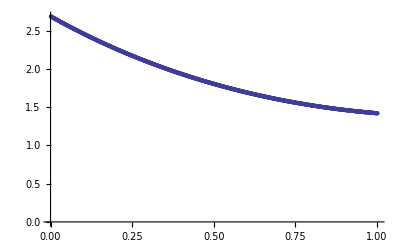

```mathematica
p1=ListPlot[tabT]
```

```mathematica
tabu1=Table[{i*0.01,Exp[1-i*0.01]},{i,1,66}];
tabu2=Table[{i*0.01,Exp[1-i*0.01]},{i,67,101}];
tabu=Join[tabu1,tabu2];
```

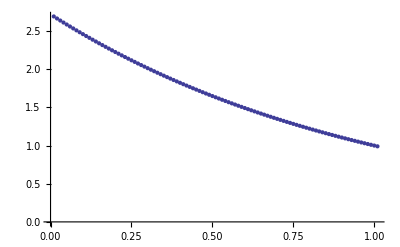

```mathematica
p2=ListPlot[tabu]
```

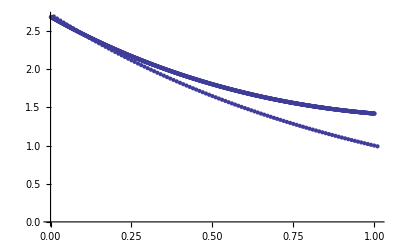

```mathematica
Show[p2,p1]
```

```mathematica
str2=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,28]

```mathematica
strList2=ReadList[str2]
```

{1.49064,1.4895,1.48837,1.48723,1.4861,1.48497,1.48384,1.48272,1.48159,1.48047,1.47934,1.47822,1.4771,1.47599,1.47487,1.47375,1.47264,1.47153,1.47042,1.46931,1.4682,1.46709,1.46599,1.46489,1.46379,1.46269,1.46159,1.46049,1.45939,1.4583,1.45721,1.45612,1.45503,1.45394,1.45285,1.45177,1.45069,1.4496,1.44852,1.44744,1.44637,1.44529,1.44422,1.44314,1.44207,1.441,1.43993,1.43887,1.4378,1.43674,1.43568,1.43461,1.43354,1.43103,1.42852,1.42602,1.42352,1.42102,1.41852,1.41602,1.41353,1.41103,1.40854,1.40605,1.40356,1.40107,1.39859,1.3961,1.39362,1.39114,1.38866,1.38618,1.3837,1.38123,1.37876,1.37628,1.37381,1.37135,1.36888,1.36641,1.36395,1.36149,1.35903,1.35657,1.35411,1.35165,1.3492,1.34674,1.34429,1.34184,1.33939,1.33694,1.3345,1.33205,1.32961,1.32717,1.32473,1.32229,1.31985,1.31742,1.31498,1.31255,1.31012,1.30769,1.30526,1.30283,1.30041,1.29798,1.29556,1.29314,1.29086,1.28902,1.28719,1.28536,1.28353,1.2817,1.27987,1.27804,1.27622,1.27439,1.27257,1.27075,1.26893,1.26711,1.26529,1.26347,1.26165,1.25984,1.25802,1.25621,1.2544,1.25259,1.25078,1.24897,1.24717,1.24536,1.24355,1.24175,1.23995,1.23815,1.23635,1.23455,1.23275,1.23095,1.22916,1.22737,1.22557,1.22378,1.22199,1.2202,1.21841,1.21662,1.21484,1.21305,1.21127,1.20949,1.2077,1.20592,1.20414,1.20237,1.20059,1.19881,1.19704,1.19526,1.19349,1.19172,1.18995,1.18818,1.18641,1.18464,1.18288,1.18111,1.17935,1.17759,1.17582,1.17406,1.1723,1.17055,1.16879,1.16703,1.16528,1.16352,1.16177,1.16002,1.15827,1.15652,1.15477,1.15302,1.15127,1.14953,1.14778,1.14604,1.1443,1.14256,1.14082,1.13908,1.13734,1.1356,1.13387,1.13213,1.1304,1.12866,1.12693,1.1252,1.12347,1.12174,1.12002,1.11829,1.11656,1.11484,1.11312,1.11139,1.10967,1.10795,1.10623,1.10451,1.1028,1.10108,1.09936,1.09765,1.09594,1.09423,1.09251,1.0908,1.08909,1.08739,1.08568,1.08397,1.08227,1.08056,1.07886,1.07716,1.07546,1.07376,1.07206,1.07036,1.06866,1.06697,1.06527,1.06358,1.06188,1.06019,1.0585,1.05681,1.05512,1.05343,1.05174,1.05006,1.04837,1.04669,1.045,1.04332,1.04164,1.03996,1.03828,1.0366,1.03492,1.03324,1.03157,1.02989,1.02822,1.02655,1.02487,1.0232,1.02153,1.01986,1.01819,1.01653,1.01486,1.0132,1.01153,1.00987,1.0082,1.00654,1.00488,1.00322,1.00156,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.998727,0.997031,0.995336,0.993642,0.991948,0.990256,0.988564,0.986874,0.985184,0.983495,0.981807,0.98012,0.978434,0.976748,0.975064,0.97338,0.971697,0.970016,0.968334,0.966654,0.964975,0.963297,0.961619,0.959942,0.958266,0.956591,0.954917,0.953244,0.951571,0.9499,0.948735,0.947747,0.94676,0.945774,0.944787,0.943801,0.942815,0.94183,0.940845,0.93986,0.938875,0.937891,0.936907,0.935923,0.934939,0.933956,0.932973,0.931991,0.931009,0.930027,0.929045,0.928064,0.927083,0.926102,0.925121,0.924141,0.923161,0.922182,0.921202,0.920223,0.919245,0.918266,0.917288,0.91631,0.915333,0.914356,0.913379,0.912402,0.911426,0.91045,0.909474,0.908499,0.907524,0.906549,0.905574,0.9046,0.903626,0.902652,0.901679,0.900706,0.899733,0.898761,0.897789,0.896817,0.895845,0.894874,0.893903,0.892932,0.891962,0.890992,0.890022,0.889052,0.888083,0.887114,0.886146,0.885177,0.884209,0.883241,0.882274,0.881307,0.88034,0.879373,0.878407,0.877441,0.876475,0.87551,0.874545,0.87358,0.872616,0.871651,0.870687,0.869724,0.86876,0.867797,0.866835,0.865872,0.86491,0.863948,0.862986,0.862025,0.861064,0.860103,0.859143,0.858183,0.857223,0.856263,0.855304,0.854345,0.853386,0.852428,0.85147,0.850512,0.849555,0.848597,0.84764,0.846684,0.845727,0.844771,0.843816,0.84286,0.841905,0.84095,0.839995,0.839041,0.838087,0.837133,0.83618,0.835226,0.834273,0.833321,0.832368,0.831416,0.830465,0.829513,0.828562,0.827611,0.82666,0.82571,0.82476,0.82381,0.822861,0.821911,0.820962,0.820014,0.819065,0.818117,0.817169,0.816222,0.815275,0.814328,0.813381,0.812435,0.811489,0.810543,0.809597,0.808652,0.807707,0.806762,0.805818,0.804874,0.80393,0.802986,0.802043,0.8011,0.800157,0.799215,0.798272,0.79733,0.796389,0.795447,0.794506,0.793565,0.792625,0.791685,0.790745,0.789805,0.788865,0.787926,0.786987,0.786049,0.78511,0.784172,0.783235,0.782297,0.78136,0.780423,0.779486,0.77855,0.777613,0.776678,0.775742,0.774807,0.773871,0.772937,0.772002,0.771068,0.770134,0.7692,0.768266,0.767333,0.7664,0.765468,0.764535,0.763603,0.762671,0.76174,0.760808,0.76012,0.759856,0.75959,0.759324,0.759058,0.758791,0.758524,0.758257,0.757989,0.757721,0.757452,0.757183,0.756913,0.756643,0.756373,0.756102,0.755831,0.75556,0.755288,0.755015,0.754742,0.754469,0.754196,0.753922,0.753647,0.753373,0.753097,0.752822,0.752546,0.75227,0.751993,0.751716,0.751438,0.751161,0.750882,0.750604,0.750325,0.750045,0.749766,0.749485,0.749205,0.748924,0.748643,0.748361,0.748079,0.747797,0.747514,0.747231,0.746948,0.746664,0.74638,0.746095,0.74581,0.745525,0.745239,0.744953,0.744667,0.74438,0.744093,0.743806,0.743518,0.74323,0.742941,0.742652,0.742363,0.742074,0.741784,0.741494,0.741203,0.740912,0.740621,0.740329,0.740038,0.739745,0.739453,0.73916,0.738867,0.738573,0.738279,0.737985,0.73769,0.737395,0.7371,0.736804,0.736509,0.736212,0.735916,0.735619,0.735322,0.735024,0.734726,0.734428,0.73413,0.733831,0.733532,0.733232,0.732933,0.732633,0.732332,0.732032,0.731731,0.731429,0.731128,0.730826,0.730524,0.730221,0.729918,0.729615,0.729312,0.729008,0.728704,0.7284,0.728095,0.72779,0.727485,0.72718,0.726874,0.726568,0.726261,0.725955,0.725648,0.72534,0.725033,0.724725,0.724417,0.724108,0.7238,0.723491,0.723181,0.722872,0.722562,0.722252,0.721941,0.721631,0.72132,0.721008,0.720697,0.720385,0.720073,0.719761,0.719448,0.719135,0.718822,0.718509,0.718195,0.717881,0.717567,0.717252,0.716937,0.716622,0.716307,0.715992,0.715676,0.71536,0.715043,0.714727,0.71441,0.714093,0.713775,0.713458,0.71314,0.712821,0.712503,0.712184,0.711865,0.711546,0.711227,0.710907,0.710587,0.710267,0.709947,0.709626,0.709305,0.708984,0.708662,0.708341,0.708019,0.707697,0.707374,0.707051,0.706729,0.706405,0.706082,0.705758,0.705435,0.705111,0.704786,0.704462,0.704137,0.703812,0.703486,0.703161,0.702835,0.702509,0.702183,0.701857,0.70153,0.701203,0.700876,0.700549,0.700221,0.699893,0.699565,0.699237,0.698908,0.69858,0.698251,0.697922,0.697592,0.697263,0.696933,0.696603,0.696272,0.695942,0.695611,0.69528,0.694949,0.694618,0.694286,0.693954,0.693622,0.69329,0.692958,0.692625,0.692292,0.691959,0.691626,0.691292,0.690959,0.690625,0.690291,0.689956,0.689622,0.689287,0.688952,0.688617,0.688282,0.687946,0.68761,0.687274,0.686938,0.686602,0.686265,0.685928,0.685591,0.685254,0.684917,0.684579,0.684241,0.683903,0.683565,0.683227,0.682888,0.682549,0.68221,0.681871,0.681532,0.681192,0.680853,0.680513,0.680173,0.679832,0.679492,0.679151,0.67881,0.678469,0.678128,0.677786,0.677445,0.677103,0.676761,0.676418,0.676076,0.675733,0.675391,0.675048,0.674705,0.674361,0.674018,0.673674,0.67333,0.672986,0.672642,0.672297,0.671953,0.671608,0.671263,0.670918,0.670572,0.670227,0.669881,0.669535,0.669189,0.668843,0.668497,0.66815,0.667803,0.667456,0.667109,0.666762,0.666414,0.666067,0.665719,0.665371,0.665023,0.664674,0.664326,0.663977,0.663628,0.663279,0.66293,0.662581,0.662231,0.661882,0.661532,0.661182,0.660831,0.660481,0.66013,0.65978,0.659429,0.659078,0.658727,0.658375,0.658024,0.657672,0.65732,0.656968,0.656616,0.656263,0.655911,0.655558,0.655205,0.654852,0.654499,0.654146,0.653792,0.653438,0.653085,0.652731,0.652376,0.652022,0.651668,0.651313,0.650958,0.650603,0.650248,0.649893,0.649537,0.649182,0.648826,0.64847,0.648114,0.647758,0.647401,0.647045,0.646688,0.646331,0.645974,0.645617,0.645259,0.644902,0.644544,0.644187,0.643829,0.64347,0.643112,0.642754,0.642395,0.642036,0.641678,0.641318,0.640959,0.6406,0.64024,0.639881,0.639521,0.639161,0.638801,0.638441,0.63808,0.63772,0.637359,0.636998,0.636637,0.636276,0.635914,0.635553,0.635191,0.63483,0.634468,0.634106,0.633743,0.633381,0.633018,0.632656,0.632293,0.63193,0.631567,0.631204,0.63084,0.630477,0.630113,0.629749,0.629385,0.629021,0.628657,0.628292,0.627928,0.627563,0.627198,0.626833,0.626468,0.626102,0.625737,0.625371,0.625005,0.624639,0.624273,0.623907,0.623541,0.623174,0.622808,0.622441,0.622074,0.621707,0.62134,0.620972,0.620605,0.620237,0.619869,0.619501,0.619133,0.618765,0.618396,0.618028,0.617659,0.61729,0.616921,0.616552,0.616183,0.615813,0.615444,0.615074,0.614704,0.614334,0.613964,0.613594,0.613223,0.612853,0.612482,0.612111,0.61174,0.611369,0.610998,0.610626,0.610255,0.609883,0.609511,0.609139,0.608767,0.608394,0.608022,0.607649,0.607277,0.606904,0.606531}

```mathematica
strList2={1.4906362197,1.4895003168,1.4883658891,1.4872329386,1.4861014669,1.4849714758,1.4838429671,1.4827159427,1.4815904042,1.4804663536,1.4793437926,1.478222723,1.4771031466,1.4759850653,1.4748684808,1.473753395,1.4726398097,1.4715277267,1.4704171479,1.469308075,1.4682005099,1.4670944544,1.4659899104,1.4648868797,1.4637853642,1.4626853635,1.4615868768,1.4604899031,1.4593944415,1.4583004912,1.4572080512,1.4561171208,1.455027699,1.4539397849,1.4528533777,1.4517684765,1.4506850805,1.4496031889,1.4485228007,1.4474439152,1.4463665314,1.4452906487,1.444216266,1.4431433828,1.442071998,1.4410021109,1.4399337208,1.4388668267,1.4378014279,1.4367375237,1.4356751131,1.4346141956,1.43353576,1.4310287537,1.4285234031,1.4260197031,1.423517649,1.4210172357,1.4185184584,1.4160213122,1.4135257922,1.4110318935,1.4085396113,1.4060489406,1.4035598767,1.4010724145,1.3985865493,1.3961022762,1.3936195903,1.3911384867,1.3886589607,1.3861810073,1.3837046218,1.3812297992,1.3787565347,1.3762848235,1.3738146607,1.3713460416,1.3688789612,1.3664134148,1.3639493976,1.3614869047,1.3590259312,1.3565664725,1.3541085237,1.3516520799,1.3491971364,1.3467436908,1.3442917381,1.3418412738,1.3393922928,1.3369447905,1.334498762,1.3320542026,1.3296111074,1.3271694717,1.3247292907,1.3222905597,1.3198532745,1.3174174322,1.3149830298,1.3125500642,1.3101185323,1.3076884312,1.3052597577,1.3028325089,1.3004066818,1.2979822732,1.2955592802,1.2931376998,1.2908563953,1.2890222212,1.2871892518,1.2853574852,1.2835269196,1.2816975533,1.2798693846,1.2780424115,1.2762166324,1.2743920455,1.272568649,1.2707464411,1.26892542,1.267105584,1.2652869312,1.26346946,1.2616531686,1.2598380551,1.2580241178,1.2562113549,1.2543997647,1.2525893453,1.2507800951,1.2489720122,1.2471650948,1.2453593413,1.2435547498,1.2417513186,1.2399490459,1.2381479298,1.2363479688,1.234549161,1.2327515046,1.2309549978,1.229159639,1.2273654263,1.2255723579,1.2237804322,1.2219896474,1.2202000016,1.2184114931,1.2166241202,1.2148378811,1.2130527741,1.2112687973,1.209485949,1.2077042275,1.205923631,1.2041441578,1.202365806,1.200588574,1.1988124599,1.197037462,1.1952635787,1.193490808,1.1917191482,1.1899485976,1.1881791545,1.186410817,1.1846435835,1.1828774522,1.1811124212,1.179348489,1.1775856536,1.1758239134,1.1740632666,1.1723037114,1.1705452462,1.1687878691,1.1670315784,1.1652763724,1.1635222492,1.1617692072,1.1600172446,1.1582663597,1.1565165506,1.1547678157,1.1530201532,1.1512735614,1.1495280384,1.1477835827,1.1460401923,1.1442978656,1.1425566008,1.1408163962,1.13907725,1.1373391605,1.1356021259,1.1338661445,1.1321312145,1.1303973343,1.128664502,1.1269327158,1.1252019742,1.1234722753,1.1217436173,1.1200159985,1.1182894173,1.1165638718,1.1148393602,1.113115881,1.1113934322,1.1096720122,1.1079516192,1.1062322515,1.1045139074,1.102796585,1.1010802827,1.0993649987,1.0976507313,1.0959374787,1.0942252392,1.092514011,1.0908037924,1.0890945817,1.0873863771,1.0856791769,1.0839729794,1.0822677827,1.0805635852,1.0788603851,1.0771581807,1.0754569702,1.0737567519,1.0720575241,1.0703592849,1.0686620328,1.0669657659,1.0652704825,1.0635761808,1.0618828592,1.0601905158,1.058499149,1.0568087569,1.0551193379,1.0534308903,1.0517434122,1.0500569019,1.0483713578,1.046686778,1.0450031608,1.0433205045,1.0416388073,1.0399580675,1.0382782834,1.0365994532,1.0349215752,1.0332446476,1.0315686688,1.0298936369,1.0282195502,1.026546407,1.0248742055,1.023202944,1.0215326208,1.0198632341,1.0181947822,1.0165272634,1.0148606758,1.0131950178,1.0115302876,1.0098664835,1.0082036037,1.0065416466,1.0048806103,1.0032204931,1.0015612933,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.9987270418,0.9970310473,0.995335947,0.9936417392,0.991948422,0.9902559935,0.988564452,0.9868737956,0.9851840225,0.983495131,0.9818071191,0.9801199851,0.9784337271,0.9767483434,0.975063832,0.9733801912,0.9716974192,0.9700155142,0.9683344742,0.9666542976,0.9649749824,0.9632965268,0.9616189291,0.9599421874,0.9582662999,0.9565912647,0.9549170801,0.9532437441,0.9515712551,0.9498996111,0.9487346597,0.9477473574,0.9467603519,0.9457736433,0.9447872316,0.9438011168,0.942815299,0.9418297781,0.9408445542,0.9398596272,0.9388749973,0.9378906643,0.9369066284,0.9359228895,0.9349394476,0.9339563027,0.9329734548,0.9319909039,0.9310086501,0.9300266932,0.9290450334,0.9280636705,0.9270826046,0.9261018356,0.9251213636,0.9241411884,0.9231613102,0.9221817288,0.9212024443,0.9202234566,0.9192447657,0.9182663715,0.9172882741,0.9163104733,0.9153329692,0.9143557617,0.9133788508,0.9124022364,0.9114259184,0.9104498969,0.9094741718,0.908498743,0.9075236104,0.9065487741,0.905574234,0.9045999899,0.9036260419,0.9026523898,0.9016790337,0.9007059734,0.8997332089,0.89876074,0.8977885668,0.8968166892,0.895845107,0.8948738202,0.8939028287,0.8929321325,0.8919617314,0.8909916253,0.8900218142,0.889052298,0.8880830766,0.8871141498,0.8861455176,0.8851771799,0.8842091367,0.8832413876,0.8822739328,0.881306772,0.8803399052,0.8793733323,0.8784070531,0.8774410675,0.8764753754,0.8755099767,0.8745448713,0.873580059,0.8726155397,0.8716513133,0.8706873797,0.8697237387,0.8687603902,0.8677973341,0.8668345702,0.8658720984,0.8649099185,0.8639480305,0.8629864341,0.8620251292,0.8610641157,0.8601033934,0.8591429622,0.8581828219,0.8572229724,0.8562634134,0.8553041449,0.8543451667,0.8533864786,0.8524280804,0.851469972,0.8505121533,0.8495546239,0.8485973839,0.8476404329,0.8466837709,0.8457273976,0.8447713128,0.8438155165,0.8428600083,0.8419047881,0.8409498557,0.839995211,0.8390408537,0.8380867836,0.8371330006,0.8361795044,0.8352262949,0.8342733718,0.833320735,0.8323683842,0.8314163192,0.8304645398,0.8295130458,0.8285618371,0.8276109133,0.8266602743,0.8257099198,0.8247598496,0.8238100635,0.8228605614,0.8219113428,0.8209624077,0.8200137558,0.8190653868,0.8181173005,0.8171694968,0.8162219753,0.8152747358,0.8143277781,0.8133811019,0.8124347069,0.8114885931,0.81054276,0.8095972074,0.8086519351,0.8077069428,0.8067622304,0.8058177974,0.8048736437,0.8039297689,0.8029861729,0.8020428554,0.801099816,0.8001570546,0.7992145708,0.7982723644,0.7973304351,0.7963887826,0.7954474067,0.794506307,0.7935654833,0.7926249353,0.7916846628,0.7907446653,0.7898049427,0.7888654946,0.7879263208,0.7869874209,0.7860487946,0.7851104418,0.7841723619,0.7832345549,0.7822970202,0.7813597577,0.7804227671,0.7794860479,0.7785496,0.7776134229,0.7766775164,0.7757418802,0.7748065139,0.7738714172,0.7729365898,0.7720020314,0.7710677416,0.7701337201,0.7691999666,0.7682664808,0.7673332622,0.7664003106,0.7654676257,0.764535207,0.7636030543,0.7626711672,0.7617395453,0.7608081884,0.7601204658,0.7598555088,0.7595901288,0.759324327,0.7590581048,0.7587914634,0.7585244043,0.7582569287,0.7579890379,0.7577207332,0.757452016,0.7571828875,0.756913349,0.7566434018,0.7563730473,0.7561022866,0.755831121,0.755559552,0.7552875806,0.7550152082,0.754742436,0.7544692654,0.7541956975,0.7539217336,0.753647375,0.7533726229,0.7530974785,0.7528219431,0.752546018,0.7522697043,0.7519930033,0.7517159161,0.7514384441,0.7511605885,0.7508823504,0.750603731,0.7503247317,0.7500453535,0.7497655976,0.7494854653,0.7492049578,0.7489240762,0.7486428217,0.7483611956,0.7480791989,0.7477968329,0.7475140986,0.7472309974,0.7469475303,0.7466636986,0.7463795032,0.7460949455,0.7458100266,0.7455247476,0.7452391096,0.7449531138,0.7446667613,0.7443800533,0.7440929908,0.743805575,0.7435178071,0.7432296881,0.7429412191,0.7426524013,0.7423632357,0.7420737235,0.7417838658,0.7414936636,0.7412031181,0.7409122303,0.7406210013,0.7403294322,0.7400375241,0.7397452781,0.7394526952,0.7391597765,0.738866523,0.7385729359,0.7382790161,0.7379847648,0.7376901829,0.7373952716,0.7371000318,0.7368044646,0.7365085711,0.7362123523,0.7359158092,0.7356189428,0.7353217542,0.7350242444,0.7347264144,0.7344282651,0.7341297977,0.7338310132,0.7335319124,0.7332324965,0.7329327664,0.7326327231,0.7323323677,0.732031701,0.7317307242,0.731429438,0.7311278437,0.730825942,0.730523734,0.7302212206,0.7299184029,0.7296152817,0.7293118581,0.729008133,0.7287041072,0.7283997819,0.7280951579,0.7277902361,0.7274850175,0.7271795031,0.7268736937,0.7265675904,0.7262611939,0.7259545053,0.7256475254,0.7253402552,0.7250326956,0.7247248475,0.7244167118,0.7241082894,0.7237995811,0.723490588,0.7231813108,0.7228717505,0.722561908,0.7222517841,0.7219413797,0.7216306958,0.7213197331,0.7210084925,0.7206969749,0.7203851812,0.7200731123,0.7197607689,0.719448152,0.7191352623,0.7188221008,0.7185086683,0.7181949656,0.7178809936,0.7175667531,0.7172522449,0.7169374698,0.7166224288,0.7163071226,0.715991552,0.7156757178,0.7153596209,0.7150432621,0.7147266422,0.7144097619,0.7140926221,0.7137752237,0.7134575673,0.7131396537,0.7128214838,0.7125030584,0.7121843782,0.711865444,0.7115462566,0.7112268168,0.7109071252,0.7105871828,0.7102669903,0.7099465483,0.7096258578,0.7093049194,0.7089837338,0.708662302,0.7083406245,0.7080187021,0.7076965356,0.7073741257,0.7070514732,0.7067285787,0.706405443,0.7060820669,0.705758451,0.7054345961,0.7051105029,0.7047861721,0.7044616044,0.7041368005,0.7038117611,0.703486487,0.7031609787,0.7028352372,0.7025092629,0.7021830566,0.701856619,0.7015299508,0.7012030527,0.7008759252,0.7005485692,0.7002209853,0.6998931741,0.6995651364,0.6992368727,0.6989083838,0.6985796703,0.6982507328,0.697921572,0.6975921886,0.6972625832,0.6969327565,0.696602709,0.6962724415,0.6959419545,0.6956112487,0.6952803247,0.6949491832,0.6946178247,0.6942862499,0.6939544595,0.6936224539,0.6932902339,0.6929578001,0.6926251529,0.6922922932,0.6919592214,0.6916259381,0.691292444,0.6909587396,0.6906248255,0.6902907024,0.6899563707,0.6896218311,0.6892870842,0.6889521305,0.6886169706,0.688281605,0.6879460344,0.6876102593,0.6872742802,0.6869380978,0.6866017125,0.686265125,0.6859283357,0.6855913453,0.6852541542,0.684916763,0.6845791722,0.6842413825,0.6839033942,0.683565208,0.6832268244,0.6828882438,0.6825494669,0.6822104941,0.681871326,0.681531963,0.6811924057,0.6808526546,0.6805127101,0.6801725729,0.6798322433,0.6794917219,0.6791510093,0.6788101057,0.6784690119,0.6781277282,0.6777862551,0.6774445931,0.6771027427,0.6767607044,0.6764184786,0.6760760659,0.6757334666,0.6753906812,0.6750477102,0.6747045541,0.6743612133,0.6740176883,0.6736739794,0.6733300873,0.6729860122,0.6726417548,0.6722973152,0.6719526942,0.671607892,0.6712629091,0.6709177459,0.6705724028,0.6702268804,0.6698811789,0.6695352988,0.6691892406,0.6688430046,0.6684965913,0.668150001,0.6678032342,0.6674562913,0.6671091726,0.6667618786,0.6664144097,0.6660667662,0.6657189485,0.6653709571,0.6650227923,0.6646744545,0.664325944,0.6639772613,0.6636284067,0.6632793806,0.6629301833,0.6625808153,0.6622312769,0.6618815684,0.6615316902,0.6611816426,0.6608314261,0.6604810409,0.6601304875,0.6597797661,0.659428877,0.6590778207,0.6587265975,0.6583752077,0.6580236516,0.6576719296,0.6573200419,0.656967989,0.6566157711,0.6562633885,0.6559108416,0.6555581307,0.655205256,0.654852218,0.6544990169,0.6541456529,0.6537921265,0.6534384379,0.6530845873,0.6527305752,0.6523764017,0.6520220672,0.6516675719,0.6513129162,0.6509581003,0.6506031244,0.6502479889,0.6498926941,0.6495372402,0.6491816274,0.648825856,0.6484699264,0.6481138387,0.6477575932,0.6474011902,0.6470446299,0.6466879125,0.6463310384,0.6459740077,0.6456168207,0.6452594776,0.6449019787,0.6445443242,0.6441865143,0.6438285493,0.6434704294,0.6431121547,0.6427537256,0.6423951423,0.6420364049,0.6416775137,0.6413184688,0.6409592706,0.6405999191,0.6402404147,0.6398807574,0.6395209476,0.6391609853,0.6388008709,0.6384406044,0.638080186,0.637719616,0.6373588946,0.6369980219,0.636636998,0.6362758232,0.6359144977,0.6355530215,0.6351913949,0.6348296181,0.6344676912,0.6341056143,0.6337433877,0.6333810114,0.6330184856,0.6326558105,0.6322929863,0.631930013,0.6315668908,0.6312036199,0.6308402003,0.6304766323,0.630112916,0.6297490514,0.6293850387,0.6290208781,0.6286565696,0.6282921134,0.6279275096,0.6275627583,0.6271978597,0.6268328138,0.6264676207,0.6261022805,0.6257367934,0.6253711595,0.6250053788,0.6246394514,0.6242733775,0.6239071571,0.6235407903,0.6231742772,0.6228076179,0.6224408124,0.6220738609,0.6217067634,0.62133952,0.6209721307,0.6206045956,0.6202369149,0.6198690884,0.6195011164,0.6191329989,0.6187647359,0.6183963274,0.6180277736,0.6176590745,0.61729023,0.6169212404,0.6165521055,0.6161828255,0.6158134003,0.6154438301,0.6150741148,0.6147042545,0.6143342491,0.6139640988,0.6135938035,0.6132233633,0.6128527781,0.6124820481,0.6121111731,0.6117401532,0.6113689885,0.6109976788,0.6106262243,0.6102546248,0.6098828805,0.6095109913,0.6091389572,0.6087667782,0.6083944542,0.6080219853,0.6076493714,0.6072766125,0.6069037086,0.6065306597};
```

```mathematica
tabT2=Table[{i*0.001,strList2[[i]]},{i,1,1001}];
```

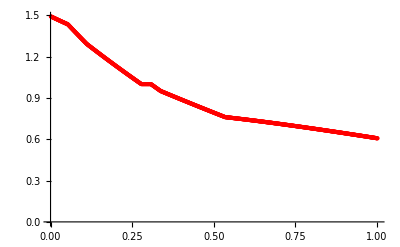

```mathematica
p12=ListPlot[tabT2,PlotStyle->Red]
```

```mathematica
tabu12=Table[{i*0.01,Exp[0.5-i*0.01]},{i,1,66}];
tabu22=Table[{i*0.01,Exp[0.5-i*0.01]},{i,67,101}];
tabu2=Join[tabu12,tabu22];
```

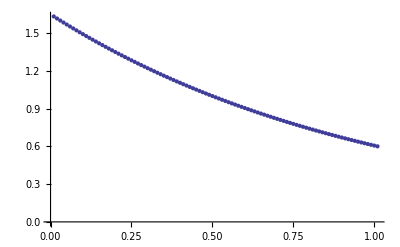

```mathematica
p22=ListPlot[tabu2]
```

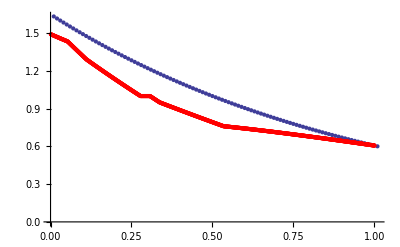

```mathematica
Show[p22,p12]
```

### alfa = 8/10

```mathematica
str3=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,23]

```mathematica
strList3=ReadList[str3]
```

{2.51145,2.50605,2.50067,2.49529,2.48993,2.48458,2.47923,2.4739,2.46858,2.46327,2.45797,2.45268,2.44739,2.44212,2.43686,2.43161,2.42638,2.42115,2.41593,2.41072,2.40552,2.40033,2.39515,2.38998,2.38483,2.37968,2.37454,2.36941,2.36429,2.35918,2.35409,2.349,2.34392,2.33885,2.33379,2.32874,2.3237,2.31867,2.31365,2.30864,2.30364,2.29865,2.29367,2.2887,2.28374,2.27879,2.27385,2.26891,2.26399,2.25908,2.25417,2.24928,2.24439,2.23952,2.23465,2.2298,2.22495,2.22011,2.21528,2.21046,2.20565,2.20085,2.19606,2.19128,2.18651,2.18174,2.17699,2.17224,2.16751,2.16278,2.15806,2.15335,2.14865,2.14396,2.13928,2.13461,2.12994,2.12529,2.12064,2.11601,2.11138,2.10676,2.10215,2.09755,2.09295,2.08837,2.0838,2.07923,2.07467,2.07012,2.06558,2.06105,2.05653,2.05202,2.04751,2.04301,2.03853,2.03405,2.02958,2.02511,2.02066,2.01621,2.01178,2.00735,2.00293,1.99852,1.99412,1.98972,1.98533,1.98096,1.97659,1.97223,1.96787,1.96353,1.95919,1.95486,1.95054,1.94623,1.94193,1.93763,1.93335,1.92907,1.9248,1.92053,1.91628,1.91203,1.90779,1.90356,1.89934,1.89513,1.89092,1.88672,1.88253,1.87835,1.87417,1.87001,1.86585,1.8617,1.85755,1.85342,1.84929,1.84517,1.84106,1.83695,1.83286,1.82877,1.82468,1.82061,1.81655,1.81249,1.80844,1.80439,1.80036,1.79633,1.79231,1.7883,1.78429,1.78029,1.7763,1.77232,1.76835,1.76438,1.76042,1.75646,1.75252,1.74858,1.74465,1.74072,1.73681,1.7329,1.729,1.7251,1.72122,1.71734,1.71346,1.7096,1.70574,1.70189,1.69804,1.69421,1.69038,1.68656,1.68274,1.67893,1.67513,1.67134,1.66755,1.66377,1.66,1.65623,1.65247,1.64872,1.64497,1.64123,1.6375,1.63378,1.63006,1.62635,1.62264,1.61895,1.61526,1.61157,1.6079,1.60423,1.60056,1.59691,1.59326,1.58961,1.58598,1.58235,1.57872,1.57511,1.5715,1.56789,1.5643,1.56071,1.55712,1.55354,1.54997,1.54641,1.54285,1.5393,1.53576,1.53222,1.52869,1.52516,1.52164,1.51813,1.51462,1.51112,1.50763,1.50414,1.50066,1.49719,1.49372,1.49026,1.4868,1.48335,1.47991,1.47647,1.47304,1.46962,1.4662,1.46279,1.45938,1.45598,1.45259,1.4492,1.44582,1.44244,1.43908,1.43571,1.43235,1.429,1.42566,1.42232,1.41899,1.41566,1.41234,1.40902,1.40571,1.40241,1.39911,1.39582,1.39253,1.38925,1.38598,1.38271,1.37945,1.37619,1.37294,1.36969,1.36645,1.36322,1.35999,1.35677,1.35355,1.35034,1.34714,1.34394,1.34074,1.33755,1.33437,1.33119,1.32802,1.32486,1.3217,1.31854,1.31539,1.31225,1.30911,1.30598,1.30285,1.29973,1.29661,1.2935,1.29039,1.28729,1.2842,1.28111,1.27803,1.27495,1.27187,1.26881,1.26574,1.26269,1.25964,1.25659,1.25355,1.25051,1.24748,1.24445,1.24143,1.23842,1.23541,1.2324,1.2294,1.22641,1.22342,1.22044,1.21746,1.21448,1.21151,1.20855,1.20559,1.20264,1.19969,1.19675,1.19381,1.19087,1.18795,1.18502,1.1821,1.17919,1.17628,1.17338,1.17048,1.16758,1.1647,1.16181,1.15893,1.15606,1.15319,1.15032,1.14746,1.14461,1.14176,1.13891,1.13607,1.13324,1.1304,1.12758,1.12476,1.12194,1.11913,1.11632,1.11352,1.11072,1.10792,1.10514,1.10235,1.09957,1.0968,1.09403,1.09126,1.0885,1.08574,1.08299,1.08024,1.0775,1.07476,1.07203,1.0693,1.06657,1.06385,1.06113,1.05842,1.05572,1.05301,1.05031,1.04762,1.04493,1.04224,1.03956,1.03689,1.03421,1.03155,1.02888,1.02622,1.02357,1.02092,1.01827,1.01563,1.01299,1.01036,1.00773,1.0051,1.00248,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.998938,0.996281,0.993627,0.990978,0.988333,0.985693,0.983056,0.980424,0.977795,0.975171,0.972551,0.969935,0.967323,0.964715,0.962111,0.959512,0.956916,0.954324,0.951736,0.949153,0.946573,0.943997,0.941425,0.938857,0.936293,0.933733,0.931177,0.928625,0.926077,0.923532,0.920992,0.918455,0.915922,0.913393,0.910868,0.908347,0.905829,0.903316,0.900806,0.8983,0.895797,0.893299,0.890804,0.888313,0.885825,0.883342,0.880862,0.878385,0.875913,0.873444,0.870979,0.868517,0.866059,0.863605,0.861154,0.858707,0.856264,0.853824,0.851387,0.848955,0.846525,0.8441,0.841678,0.839259,0.836844,0.834432,0.832024,0.82962,0.827219,0.824821,0.822427,0.820036,0.817649,0.815265,0.812885,0.810508,0.808134,0.805764,0.803397,0.801033,0.798673,0.796316,0.793963,0.791613,0.789266,0.786923,0.784582,0.782245,0.779912,0.777581,0.775254,0.77293,0.77061,0.768292,0.765978,0.763667,0.761359,0.759055,0.756753,0.754455,0.75216,0.749868,0.747579,0.745293,0.743011,0.740731,0.738455,0.736182,0.733911,0.731644,0.72938,0.727119,0.724861,0.722606,0.720354,0.718106,0.71586,0.713617,0.711377,0.70914,0.706906,0.704675,0.702447,0.700222,0.698,0.697341,0.69683,0.696318,0.695804,0.695289,0.694773,0.694256,0.693737,0.693217,0.692696,0.692173,0.691649,0.691124,0.690598,0.69007,0.689541,0.689011,0.68848,0.687947,0.687414,0.686879,0.686343,0.685805,0.685267,0.684727,0.684186,0.683644,0.6831,0.682556,0.68201,0.681463,0.680915,0.680366,0.679816,0.679264,0.678712,0.678158,0.677603,0.677047,0.67649,0.675931,0.675372,0.674811,0.67425,0.673687,0.673123,0.672558,0.671992,0.671425,0.670856,0.670287,0.669717,0.669145,0.668573,0.667999,0.667424,0.666848,0.666272,0.665694,0.665115,0.664535,0.663954,0.663372,0.662789,0.662205,0.661619,0.661033,0.660446,0.659858,0.659269,0.658678,0.658087,0.657495,0.656902,0.656308,0.655712,0.655116,0.654519,0.653921,0.653322,0.652722,0.652121,0.651519,0.650916,0.650312,0.649707,0.649101,0.648494,0.647887,0.647278,0.646668,0.646058,0.645446,0.644834,0.644221,0.643607,0.642991,0.642375,0.641758,0.64114,0.640522,0.639902,0.639281,0.63866,0.638038,0.637414,0.63679,0.636165,0.635539,0.634912,0.634285,0.633656,0.633027,0.632396,0.631765,0.631133,0.6305,0.629867,0.629232,0.628596,0.62796,0.627323,0.626685,0.626046,0.625407,0.624766,0.624125,0.623483,0.62284,0.622196,0.621551,0.620906,0.62026,0.619612,0.618965,0.618316,0.617666,0.617016,0.616365,0.615713,0.61506,0.614407,0.613752,0.613097,0.612441,0.611785,0.611127,0.610469,0.60981,0.60915,0.60849,0.607828,0.607166,0.606503,0.60584,0.605175,0.60451,0.603844,0.603177,0.60251,0.601842,0.601173,0.600503,0.599832,0.599161,0.598489,0.597816,0.597143,0.596469,0.595794,0.595118,0.594442,0.593765,0.593087,0.592408,0.591729,0.591049,0.590368,0.589686,0.589004,0.588321,0.587637,0.586953,0.586268,0.585582,0.584895,0.584208,0.58352,0.582832,0.582142,0.581452,0.580761,0.58007,0.579378,0.578685,0.577991,0.577297,0.576602,0.575906,0.57521,0.574513,0.573815,0.573117,0.572417,0.571718,0.571017,0.570316,0.569614,0.568912,0.568208,0.567504,0.5668,0.566095,0.565389,0.564682,0.563975,0.563267,0.562558,0.561849,0.561139,0.560428,0.559717,0.559005,0.558292,0.557579,0.556865,0.55615,0.555435,0.554719,0.554002,0.553285,0.552567,0.551848,0.551129,0.550409,0.549688,0.548967,0.548245,0.547523,0.546799,0.546076,0.545351,0.544626,0.5439,0.543174,0.542446,0.541719,0.54099,0.540261,0.539531,0.538801,0.53807,0.537338,0.536606,0.535873,0.535139,0.534405,0.53367,0.532934,0.532198,0.531461,0.530724,0.529986,0.529247,0.528508,0.527767,0.527027,0.526285,0.525543,0.524801,0.524057,0.523313,0.522569,0.521824,0.521078,0.520331,0.519584,0.518836,0.518088,0.517339,0.516589,0.515839,0.515088,0.514336,0.513584,0.512831,0.512077,0.511323,0.510568,0.509813,0.509057,0.5083,0.507542,0.506784,0.506026,0.505266,0.504506,0.503746,0.502984,0.502222,0.50146,0.500697,0.499933,0.499168,0.498403,0.497637,0.496871,0.496104,0.495336,0.494568,0.493798,0.493029,0.492258,0.491487,0.490716,0.489943,0.489171,0.488397,0.487623,0.486848,0.486072,0.485296,0.484519,0.483742,0.482963,0.482185,0.481405,0.480625,0.479844,0.479063,0.47828,0.477498,0.476714,0.47593,0.475145,0.47436,0.473574,0.472787,0.472,0.471211,0.470423,0.469633,0.468843,0.468052,0.467261,0.466469,0.465676,0.464882,0.464088,0.463293,0.462498,0.461702,0.460905,0.460107,0.459309,0.45851,0.45771,0.45691,0.456109,0.455307,0.454505,0.453702,0.452898,0.452094,0.451289,0.450483,0.449676,0.448869,0.448061,0.447252,0.446443,0.445633,0.444822,0.444011,0.443199,0.442386,0.441572,0.440758,0.439943,0.439127,0.438311,0.437494,0.436676,0.435857,0.435038,0.434218,0.433397,0.432576,0.431754,0.430931,0.430107,0.429283,0.428458,0.427632,0.426805,0.425978,0.42515,0.424321,0.423491,0.422661,0.42183,0.420998,0.420166,0.419332,0.418498,0.417663,0.416828,0.415991,0.415154,0.414316,0.413478,0.412638,0.411798,0.410957,0.410116,0.409273,0.40843,0.407586,0.406741,0.405895,0.405049,0.404202,0.403354,0.402505,0.401655,0.400805,0.399954,0.399102,0.398249,0.397396,0.396541,0.395686,0.39483,0.393973,0.393116,0.392257,0.391398,0.390538,0.389677,0.388815,0.387953,0.387089,0.386225,0.38536,0.384494,0.383627,0.38276,0.381891,0.381022,0.380152,0.379281,0.378409,0.377536,0.376663,0.375788,0.374913,0.374037,0.37316,0.372282,0.371403,0.370524,0.369643,0.368762,0.367879}

```mathematica
strList3={2.5114490694,2.5060535189,2.5006685303,2.4952940807,2.4899301474,2.4845767076,2.4792337389,2.4739012185,2.468579124,2.4632674327,2.4579661223,2.4526751703,2.4473945543,2.4421242521,2.4368642412,2.4316144995,2.4263750048,2.4211457349,2.4159266676,2.4107177809,2.4055190529,2.4003304613,2.3951519845,2.3899836003,2.3848252871,2.3796770229,2.374538786,2.3694105546,2.364292307,2.3591840217,2.354085677,2.3489972513,2.3439187231,2.338850071,2.3337912734,2.3287423091,2.3237031566,2.3186737946,2.3136542018,2.3086443571,2.3036442392,2.298653827,2.2936730993,2.2887020352,2.2837406135,2.2787888133,2.2738466137,2.2689139937,2.2639909325,2.2590774092,2.2541734031,2.2492788934,2.2443938595,2.2395182806,2.2346521361,2.2297954055,2.2249480682,2.2201101038,2.2152814916,2.2104622114,2.2056522427,2.2008515651,2.1960601585,2.1912780025,2.1865050768,2.1817413614,2.176986836,2.1722414805,2.1675052748,2.162778199,2.1580602331,2.1533513569,2.1486515508,2.1439607947,2.1392790688,2.1346063534,2.1299426286,2.1252878748,2.1206420722,2.1160052012,2.1113772421,2.1067581755,2.1021479817,2.0975466413,2.0929541347,2.0883704426,2.0837955456,2.0792294243,2.0746720595,2.0701234317,2.0655835219,2.0610523107,2.056529779,2.0520159077,2.0475106777,2.0430140699,2.0385260653,2.034046645,2.0295757899,2.0251134812,2.0206596999,2.0162144273,2.0117776446,2.0073493328,2.0029294735,1.9985180477,1.994115037,1.9897204225,1.9853341859,1.9809563084,1.9765867716,1.972225557,1.9678726461,1.9635280206,1.959191662,1.954863552,1.9505436724,1.9462320047,1.9419285308,1.9376332325,1.9333460915,1.9290670899,1.9247962094,1.920533432,1.9162787396,1.9120321143,1.9077935381,1.9035629931,1.8993404613,1.8951259249,1.8909193661,1.886720767,1.88253011,1.8783473772,1.874172551,1.8700056137,1.8658465478,1.8616953355,1.8575519593,1.8534164017,1.8492886453,1.8451686725,1.8410564659,1.8369520081,1.8328552817,1.8287662695,1.824684954,1.8206113181,1.8165453445,1.8124870161,1.8084363155,1.8043932258,1.8003577297,1.7963298103,1.7923094504,1.7882966331,1.7842913414,1.7802935583,1.7763032669,1.7723204504,1.7683450919,1.7643771745,1.7604166815,1.7564635961,1.7525179016,1.7485795814,1.7446486186,1.7407249968,1.7368086992,1.7328997094,1.7289980108,1.7251035869,1.7212164211,1.7173364971,1.7134637985,1.7095983088,1.7057400117,1.7018888908,1.69804493,1.6942081128,1.6903784231,1.6865558447,1.6827403613,1.6789319569,1.6751306154,1.6713363206,1.6675490564,1.663768807,1.6599955562,1.6562292881,1.6524699867,1.6487176362,1.6449722207,1.6412337243,1.6375021312,1.6337774256,1.6300595918,1.626348614,1.6226444765,1.6189471637,1.6152566598,1.6115729493,1.6078960166,1.6042258461,1.6005624224,1.5969057298,1.5932557529,1.5896124763,1.5859758845,1.5823459622,1.578722694,1.5751060646,1.5714960586,1.5678926608,1.564295856,1.5607056288,1.5571219642,1.5535448469,1.5499742618,1.5464101938,1.5428526279,1.5393015488,1.5357569418,1.5322187916,1.5286870834,1.5251618022,1.521642933,1.5181304611,1.5146243715,1.5111246494,1.5076312799,1.5041442483,1.5006635399,1.4971891398,1.4937210335,1.4902592061,1.4868036431,1.4833543299,1.4799112518,1.4764743942,1.4730437426,1.4696192826,1.4662009995,1.4627888789,1.4593829065,1.4559830677,1.4525893482,1.4492017336,1.4458202095,1.4424447618,1.439075376,1.4357120379,1.4323547332,1.4290034479,1.4256581676,1.4223188782,1.4189855656,1.4156582156,1.4123368143,1.4090213475,1.4057118011,1.4024081612,1.3991104138,1.395818545,1.3925325407,1.3892523872,1.3859780704,1.3827095765,1.3794468918,1.3761900024,1.3729388944,1.3696935542,1.366453968,1.363220122,1.3599920027,1.3567695963,1.3535528891,1.3503418677,1.3471365183,1.3439368274,1.3407427814,1.3375543669,1.3343715703,1.3311943782,1.328022777,1.3248567535,1.3216962941,1.3185413855,1.3153920143,1.3122481672,1.309109831,1.3059769922,1.3028496376,1.2997277541,1.2966113283,1.293500347,1.2903947972,1.2872946657,1.2841999393,1.2811106049,1.2780266494,1.2749480598,1.2718748231,1.2688069262,1.2657443562,1.2626871,1.2596351448,1.2565884775,1.2535470854,1.2505109555,1.247480075,1.244454431,1.2414340107,1.2384188013,1.2354087901,1.2324039643,1.2294043113,1.2264098182,1.2234204724,1.2204362612,1.217457172,1.2144831923,1.2115143093,1.2085505106,1.2055917835,1.2026381156,1.1996894943,1.1967459071,1.1938073416,1.1908737854,1.1879452259,1.1850216509,1.1821030478,1.1791894044,1.1762807084,1.1733769473,1.1704781089,1.167584181,1.1646951512,1.1618110073,1.1589317371,1.1560573285,1.1531877692,1.150323047,1.1474631499,1.1446080658,1.1417577825,1.1389122879,1.1360715701,1.1332356169,1.1304044164,1.1275779566,1.1247562254,1.121939211,1.1191269015,1.1163192848,1.1135163491,1.1107180825,1.1079244733,1.1051355094,1.1023511792,1.0995714708,1.0967963725,1.0940258724,1.0912599589,1.0884986203,1.0857418448,1.0829896207,1.0802419365,1.0774987804,1.0747601408,1.0720260062,1.0692963649,1.0665712054,1.0638505161,1.0611342856,1.0584225022,1.0557151546,1.0530122311,1.0503137205,1.0476196112,1.0449298919,1.042244551,1.0395635774,1.0368869595,1.0342146861,1.0315467458,1.0288831273,1.0262238194,1.0235688107,1.0209180901,1.0182716462,1.0156294679,1.0129915439,1.0103578632,1.0077284145,1.0051031866,1.0024821686,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.9989378884,0.9962805212,0.9936273382,0.9909783282,0.98833348,0.9856927822,0.9830562239,0.9804237936,0.9777954804,0.975171273,0.9725511604,0.9699351314,0.9673231749,0.9647152799,0.9621114354,0.9595116301,0.9569158533,0.9543240937,0.9517363405,0.9491525827,0.9465728094,0.9439970095,0.9414251722,0.9388572865,0.9362933416,0.9337333267,0.9311772307,0.928625043,0.9260767527,0.923532349,0.920991821,0.9184551581,0.9159223494,0.9133933843,0.9108682519,0.9083469417,0.9058294428,0.9033157447,0.9008058366,0.8982997079,0.8957973481,0.8932987464,0.8908038923,0.8883127752,0.8858253845,0.8833417097,0.8808617403,0.8783854657,0.8759128754,0.873443959,0.8709787059,0.8685171057,0.8660591481,0.8636048224,0.8611541184,0.8587070257,0.8562635338,0.8538236324,0.8513873111,0.8489545597,0.8465253677,0.8440997249,0.841677621,0.8392590458,0.8368439889,0.8344324401,0.8320243892,0.8296198259,0.8272187401,0.8248211216,0.8224269602,0.8200362458,0.8176489681,0.8152651171,0.8128846827,0.8105076548,0.8081340232,0.8057637779,0.8033969088,0.801033406,0.7986732593,0.7963164588,0.7939629944,0.7916128562,0.7892660342,0.7869225185,0.784582299,0.7822453659,0.7799117092,0.777581319,0.7752541855,0.7729302988,0.770609649,0.7682922262,0.7659780206,0.7636670225,0.7613592219,0.7590546092,0.7567531744,0.7544549079,0.7521597999,0.7498678406,0.7475790203,0.7452933293,0.743010758,0.7407312965,0.7384549353,0.7361816646,0.7339114749,0.7316443564,0.7293802996,0.7271192948,0.7248613325,0.722606403,0.7203544968,0.7181056043,0.715859716,0.7136168223,0.7113769138,0.7091399808,0.706906014,0.7046750037,0.7024469406,0.7002218152,0.6979996181,0.6973410566,0.6968300651,0.6963177671,0.6958041678,0.6952892723,0.6947730856,0.6942556131,0.6937368596,0.6932168304,0.6926955304,0.6921729646,0.691649138,0.6911240556,0.6905977223,0.6900701431,0.6895413229,0.6890112664,0.6884799786,0.6879474643,0.6874137282,0.6868787753,0.6863426101,0.6858052375,0.6852666622,0.6847268888,0.684185922,0.6836437664,0.6831004268,0.6825559075,0.6820102133,0.6814633487,0.6809153182,0.6803661263,0.6798157775,0.6792642762,0.6787116269,0.678157834,0.6776029019,0.677046835,0.6764896376,0.675931314,0.6753718685,0.6748113054,0.674249629,0.6736868436,0.6731229532,0.6725579621,0.6719918746,0.6714246946,0.6708564265,0.6702870741,0.6697166418,0.6691451334,0.6685725531,0.6679989049,0.6674241927,0.6668484206,0.6662715924,0.6656937122,0.6651147839,0.6645348112,0.6639537982,0.6633717486,0.6627886662,0.662204555,0.6616194186,0.6610332608,0.6604460855,0.6598578961,0.6592686966,0.6586784906,0.6580872817,0.6574950735,0.6569018697,0.6563076739,0.6557124897,0.6551163206,0.6545191701,0.6539210418,0.6533219391,0.6527218656,0.6521208246,0.6515188197,0.6509158541,0.6503119314,0.6497070549,0.6491012279,0.6484944538,0.6478867359,0.6472780774,0.6466684817,0.646057952,0.6454464915,0.6448341034,0.644220791,0.6436065573,0.6429914057,0.6423753391,0.6417583607,0.6411404735,0.6405216808,0.6399019854,0.6392813905,0.6386598991,0.6380375141,0.6374142386,0.6367900754,0.6361650275,0.6355390979,0.6349122894,0.634284605,0.6336560474,0.6330266195,0.6323963241,0.6317651641,0.6311331422,0.6305002612,0.6298665238,0.6292319328,0.6285964908,0.6279602005,0.6273230647,0.6266850859,0.6260462668,0.62540661,0.6247661181,0.6241247936,0.6234826392,0.6228396574,0.6221958506,0.6215512214,0.6209057723,0.6202595057,0.619612424,0.6189645298,0.6183158253,0.617666313,0.6170159953,0.6163648745,0.615712953,0.615060233,0.6144067169,0.6137524068,0.6130973052,0.6124414143,0.6117847362,0.6111272731,0.6104690274,0.609810001,0.6091501963,0.6084896152,0.60782826,0.6071661327,0.6065032355,0.6058395703,0.6051751392,0.6045099443,0.6038439875,0.6031772709,0.6025097964,0.601841566,0.6011725816,0.6005028451,0.5998323585,0.5991611236,0.5984891423,0.5978164165,0.5971429479,0.5964687385,0.5957937899,0.595118104,0.5944416826,0.5937645274,0.59308664,0.5924080224,0.591728676,0.5910486026,0.5903678039,0.5896862816,0.5890040371,0.5883210722,0.5876373884,0.5869529874,0.5862678706,0.5855820396,0.584895496,0.5842082412,0.5835202767,0.582831604,0.5821422246,0.5814521399,0.5807613513,0.5800698603,0.5793776681,0.5786847763,0.5779911861,0.5772968988,0.5766019159,0.5759062386,0.5752098682,0.574512806,0.5738150532,0.5731166111,0.5724174808,0.5717176637,0.5710171608,0.5703159734,0.5696141026,0.5689115496,0.5682083154,0.5675044012,0.5667998081,0.5660945372,0.5653885895,0.564681966,0.5639746678,0.5632666959,0.5625580512,0.5618487349,0.5611387477,0.5604280907,0.5597167648,0.5590047709,0.5582921099,0.5575787827,0.5568647902,0.5561501331,0.5554348124,0.5547188288,0.5540021831,0.5532848762,0.5525669087,0.5518482815,0.5511289953,0.5504090508,0.5496884487,0.5489671898,0.5482452745,0.5475227037,0.546799478,0.546075598,0.5453510643,0.5446258775,0.5439000381,0.5431735468,0.5424464041,0.5417186105,0.5409901666,0.5402610728,0.5395313296,0.5388009375,0.5380698969,0.5373382083,0.5366058722,0.5358728888,0.5351392586,0.534404982,0.5336700594,0.532934491,0.5321982773,0.5314614185,0.5307239149,0.5299857668,0.5292469744,0.5285075382,0.5277674581,0.5270267346,0.5262853678,0.5255433578,0.5248007049,0.5240574093,0.523313471,0.5225688902,0.521823667,0.5210778015,0.5203312939,0.519584144,0.5188363522,0.5180879182,0.5173388423,0.5165891244,0.5158387644,0.5150877624,0.5143361183,0.5135838322,0.5128309038,0.5120773332,0.5113231201,0.5105682647,0.5098127666,0.5090566257,0.508299842,0.5075424152,0.5067843451,0.5060256316,0.5052662743,0.5045062732,0.5037456279,0.5029843382,0.5022224038,0.5014598245,0.5006965998,0.4999327295,0.4991682133,0.4984030508,0.4976372416,0.4968707854,0.4961036817,0.4953359302,0.4945675304,0.4937984819,0.4930287843,0.492258437,0.4914874396,0.4907157916,0.4899434925,0.4891705417,0.4883969388,0.487622683,0.486847774,0.486072211,0.4852959936,0.484519121,0.4837415927,0.4829634079,0.4821845661,0.4814050666,0.4806249087,0.4798440916,0.4790626147,0.4782804772,0.4774976784,0.4767142175,0.4759300938,0.4751453064,0.4743598545,0.4735737374,0.4727869542,0.471999504,0.471211386,0.4704225993,0.4696331431,0.4688430163,0.4680522181,0.4672607476,0.4664686037,0.4656757856,0.4648822923,0.4640881227,0.4632932759,0.4624977508,0.4617015464,0.4609046616,0.4601070954,0.4593088467,0.4585099144,0.4577102974,0.4569099946,0.4561090048,0.4553073269,0.4545049598,0.4537019021,0.4528981528,0.4520937106,0.4512885743,0.4504827427,0.4496762145,0.4488689885,0.4480610633,0.4472524376,0.4464431103,0.4456330799,0.444822345,0.4440109045,0.4431987567,0.4423859005,0.4415723344,0.440758057,0.4399430668,0.4391273624,0.4383109425,0.4374938054,0.4366759497,0.435857374,0.4350380767,0.4342180562,0.4333973111,0.4325758398,0.4317536407,0.4309307123,0.4301070529,0.429282661,0.4284575348,0.4276316729,0.4268050734,0.4259777348,0.4251496554,0.4243208334,0.4234912672,0.422660955,0.4218298951,0.4209980857,0.4201655252,0.4193322116,0.4184981432,0.4176633181,0.4168277347,0.4159913909,0.415154285,0.4143164151,0.4134777793,0.4126383758,0.4117982025,0.4109572576,0.4101155391,0.4092730451,0.4084297737,0.4075857227,0.4067408903,0.4058952744,0.4050488731,0.4042016841,0.4033537056,0.4025049354,0.4016553715,0.4008050117,0.3999538539,0.3991018961,0.398249136,0.3973955716,0.3965412006,0.3956860209,0.3948300302,0.3939732264,0.3931156072,0.3922571705,0.3913979138,0.3905378351,0.3896769319,0.388815202,0.387952643,0.3870892527,0.3862250288,0.3853599687,0.3844940703,0.383627331,0.3827597485,0.3818913204,0.3810220443,0.3801519176,0.379280938,0.378409103,0.3775364101,0.3766628568,0.3757884406,0.3749131589,0.3740370092,0.373159989,0.3722820957,0.3714033267,0.3705236793,0.369643151,0.3687617392,0.3678794412};
```

```mathematica
tabT3=Table[{i*0.002,strList3[[i]]},{i,1,1001}];
```

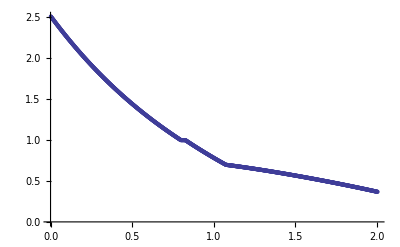

```mathematica
p13=ListPlot[tabT3]
```

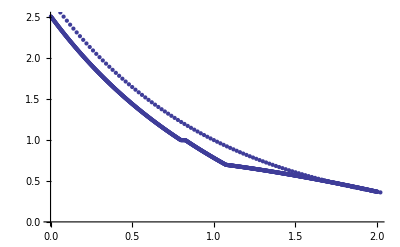

```mathematica
Show[p13,p2]
```

```mathematica
str4=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,24]

```mathematica
strList4=ReadList[str4]
```

{7.38563,7.37346,7.36131,7.34918,7.33708,7.325,7.31294,7.3009,7.28888,7.27689,7.26492,7.25297,7.24104,7.22914,7.21726,7.2054,7.19356,7.18174,7.16995,7.15817,7.14642,7.13469,7.12298,7.1113,7.09963,7.08799,7.07637,7.06477,7.05319,7.04163,7.0301,7.01858,7.00709,6.99562,6.98417,6.97274,6.96134,6.94995,6.93859,6.92724,6.91592,6.90462,6.89334,6.88208,6.87085,6.85963,6.84843,6.83726,6.8261,6.81497,6.80386,6.79277,6.7817,6.77065,6.75962,6.74861,6.73762,6.72666,6.71571,6.70478,6.69388,6.68299,6.67213,6.66129,6.65046,6.63966,6.62888,6.61812,6.60737,6.59665,6.58595,6.57527,6.56461,6.55397,6.54335,6.53275,6.52217,6.5116,6.50106,6.49054,6.48004,6.46956,6.4591,6.44866,6.43824,6.42784,6.41746,6.4071,6.39675,6.38643,6.37613,6.36584,6.35558,6.34534,6.33511,6.32491,6.31472,6.30456,6.29441,6.28428,6.27418,6.26409,6.25402,6.24397,6.23394,6.22393,6.21393,6.20396,6.19401,6.18407,6.17416,6.16426,6.15438,6.14452,6.13469,6.12486,6.11506,6.10528,6.09552,6.08577,6.07605,6.06634,6.05665,6.04698,6.03733,6.0277,6.01808,6.00849,5.99891,5.98935,5.97981,5.97029,5.96079,5.9513,5.94184,5.93239,5.92296,5.91355,5.90416,5.89479,5.88543,5.87609,5.86678,5.85747,5.84819,5.83893,5.82968,5.82045,5.81124,5.80205,5.79288,5.78372,5.77458,5.76546,5.75636,5.74728,5.73821,5.72916,5.72013,5.71112,5.70212,5.69314,5.68418,5.67524,5.66632,5.65741,5.64852,5.63965,5.6308,5.62196,5.61314,5.60434,5.59555,5.58679,5.57804,5.56931,5.56059,5.5519,5.54322,5.53455,5.52591,5.51728,5.50867,5.50008,5.4915,5.48294,5.4744,5.46587,5.45737,5.44888,5.4404,5.43195,5.42351,5.41508,5.40668,5.39829,5.38992,5.38156,5.37322,5.3649,5.3566,5.34831,5.34004,5.33178,5.32355,5.31533,5.30712,5.29893,5.29076,5.28261,5.27447,5.26635,5.25825,5.25016,5.24209,5.23403,5.22599,5.21797,5.20996,5.20197,5.194,5.18604,5.1781,5.17018,5.16227,5.15438,5.1465,5.13864,5.1308,5.12297,5.11516,5.10737,5.09959,5.09183,5.08408,5.07635,5.06863,5.06093,5.05325,5.04559,5.03793,5.0303,5.02268,5.01508,5.00749,4.99992,4.99236,4.98482,4.9773,4.96979,4.9623,4.95482,4.94736,4.93991,4.93248,4.92507,4.91767,4.91028,4.90292,4.89556,4.88823,4.88091,4.8736,4.86631,4.85903,4.85178,4.84453,4.8373,4.83009,4.82289,4.81571,4.80854,4.80139,4.79425,4.78713,4.78002,4.77293,4.76585,4.75879,4.75175,4.74471,4.7377,4.7307,4.72371,4.71674,4.70979,4.70285,4.69592,4.68901,4.68211,4.67523,4.66837,4.66151,4.65468,4.64786,4.64105,4.63426,4.62748,4.62072,4.61397,4.60724,4.60052,4.59382,4.58713,4.58045,4.57379,4.56715,4.56052,4.5539,4.5473,4.54071,4.53414,4.52759,4.52104,4.51451,4.508,4.5015,4.49501,4.48854,4.48209,4.47565,4.46922,4.4628,4.4564,4.45002,4.44365,4.43729,4.43095,4.42462,4.41831,4.41201,4.40573,4.39945,4.3932,4.38695,4.38073,4.37451,4.36831,4.36212,4.35595,4.34979,4.34365,4.33752,4.3314,4.3253,4.31921,4.31314,4.30708,4.30103,4.295,4.28898,4.28297,4.27698,4.271,4.26504,4.25909,4.25315,4.24723,4.24132,4.23543,4.22955,4.22368,4.21783,4.21199,4.20616,4.20035,4.19455,4.18876,4.18299,4.17723,4.17149,4.16575,4.16004,4.15433,4.14864,4.14296,4.1373,4.13165,4.12601,4.12039,4.11478,4.10918,4.1036,4.09803,4.09247,4.08692,4.08139,4.07588,4.07037,4.06488,4.05941,4.05394,4.04849,4.04305,4.03763,4.03222,4.02682,4.02143,4.01606,4.0107,4.00457,3.99664,3.98872,3.98082,3.97293,3.96506,3.95721,3.94938,3.94156,3.93376,3.92598,3.91821,3.91046,3.90273,3.89501,3.88732,3.87963,3.87197,3.86432,3.85669,3.84907,3.84147,3.83389,3.82632,3.81878,3.81124,3.80373,3.79623,3.78874,3.78128,3.77382,3.76639,3.75897,3.75157,3.74418,3.73681,3.72946,3.72212,3.7148,3.70749,3.7002,3.69293,3.68567,3.67843,3.6712,3.66399,3.6568,3.64962,3.64246,3.63531,3.62818,3.62106,3.61396,3.60688,3.59981,3.59275,3.58571,3.57869,3.57168,3.56469,3.55771,3.55075,3.54381,3.53687,3.52996,3.52306,3.51617,3.5093,3.50245,3.49561,3.48878,3.48197,3.47518,3.4684,3.46163,3.45488,3.44815,3.44143,3.43472,3.42803,3.42135,3.41469,3.40805,3.40141,3.3948,3.38819,3.38161,3.37503,3.36847,3.36193,3.3554,3.34888,3.34238,3.3359,3.32942,3.32297,3.31652,3.31009,3.30368,3.29728,3.29089,3.28452,3.27816,3.27182,3.26549,3.25917,3.25287,3.24658,3.24031,3.23405,3.2278,3.22157,3.21535,3.20914,3.20295,3.19678,3.19061,3.18446,3.17833,3.17221,3.1661,3.16,3.15392,3.14785,3.1418,3.13576,3.12973,3.12372,3.11772,3.11173,3.10576,3.0998,3.09385,3.08792,3.082,3.07609,3.0702,3.06582,3.06159,3.05738,3.05317,3.04897,3.04478,3.0406,3.03642,3.03226,3.02811,3.02396,3.01982,3.0157,3.01158,3.00747,3.00337,2.99928,2.99519,2.99112,2.98706,2.983,2.97896,2.97492,2.97089,2.96687,2.96286,2.95886,2.95486,2.95088,2.9469,2.94294,2.93898,2.93503,2.93109,2.92716,2.92324,2.91932,2.91542,2.91152,2.90764,2.90376,2.89989,2.89603,2.89218,2.88833,2.8845,2.88067,2.87685,2.87304,2.86924,2.86545,2.86167,2.8579,2.85413,2.85037,2.84663,2.84289,2.83915,2.83543,2.83172,2.82801,2.82432,2.82063,2.81695,2.81328,2.80961,2.80596,2.80231,2.79868,2.79505,2.79143,2.78782,2.78421,2.78062,2.77703,2.77345,2.76988,2.76632,2.76277,2.75923,2.75569,2.75216,2.74864,2.74513,2.74163,2.73814,2.73465,2.73117,2.72771,2.72424,2.72079,2.71735,2.71391,2.71048,2.70707,2.70365,2.70025,2.69686,2.69347,2.69009,2.68672,2.68336,2.68001,2.67666,2.67333,2.67,2.66668,2.66336,2.66006,2.65676,2.65347,2.65019,2.64692,2.64366,2.6404,2.63716,2.63392,2.63068,2.62746,2.62425,2.62104,2.61784,2.61465,2.61147,2.60829,2.60512,2.60197,2.59881,2.59567,2.59254,2.58941,2.58629,2.58318,2.58008,2.57698,2.57389,2.57081,2.56774,2.56468,2.56162,2.55858,2.55554,2.5525,2.54948,2.54646,2.54346,2.54046,2.53746,2.53448,2.5315,2.52853,2.52557,2.52262,2.51967,2.51673,2.5138,2.51088,2.50797,2.50506,2.50216,2.49927,2.49639,2.49351,2.49064,2.48778,2.48493,2.48209,2.47925,2.47642,2.4736,2.47078,2.46798,2.46518,2.46239,2.4596,2.45683,2.45406,2.4513,2.44855,2.4458,2.44306,2.44033,2.43761,2.4349,2.43219,2.42949,2.4268,2.42411,2.42144,2.41877,2.4161,2.41345,2.4108,2.40816,2.40553,2.40291,2.40029,2.39768,2.39508,2.39248,2.3899,2.38732,2.38475,2.38218,2.37963,2.37708,2.37453,2.372,2.36947,2.36695,2.36444,2.36193,2.35944,2.35695,2.35446,2.35199,2.34952,2.34706,2.34461,2.34216,2.33972,2.33729,2.33487,2.33245,2.33004,2.32764,2.32524,2.32286,2.32048,2.3181,2.31574,2.31338,2.31103,2.30869,2.30635,2.30402,2.3017,2.29938,2.29708,2.29478,2.29248,2.2902,2.28792,2.28565,2.28338,2.28113,2.27888,2.27663,2.2744,2.27217,2.26995,2.26774,2.26553,2.26333,2.26114,2.25895,2.25677,2.2546,2.25244,2.25028,2.24813,2.24599,2.24386,2.24173,2.23961,2.23749,2.23539,2.23329,2.23119,2.22911,2.22703,2.22496,2.22289,2.22083,2.21878,2.21674,2.2147,2.21268,2.21065,2.20864,2.20663,2.20463,2.20263,2.20065,2.19867,2.19669,2.19473,2.19277,2.19081,2.18887,2.18693,2.185,2.18307,2.18116,2.17925,2.17734,2.17544,2.17356,2.17167,2.1698,2.16793,2.16606,2.16421,2.16236,2.16052,2.15868,2.15686,2.15504,2.15322,2.15141,2.14961,2.14782,2.14603,2.14425,2.14248,2.14071,2.13896,2.1372,2.13546,2.13372,2.13199,2.13026,2.12854,2.12683,2.12513,2.12343,2.12174,2.12005,2.11838,2.1167,2.11504,2.11338,2.11173,2.11009,2.10845,2.10682,2.1052,2.10358,2.10197,2.10037,2.09877,2.09718,2.0956,2.09402,2.09245,2.09089,2.08933,2.08778,2.08624,2.0847,2.08318,2.08165,2.08014,2.07863,2.07712,2.07563,2.07414,2.07266,2.07118,2.06971,2.06825,2.06679,2.06534,2.0639,2.06246,2.06103,2.05961,2.05819,2.05678,2.05538,2.05398,2.05259,2.05121,2.04983,2.04846,2.0471,2.04574,2.04439,2.04305,2.04171,2.04038,2.03906,2.03774,2.03643,2.03513,2.03383,2.03254,2.03125,2.02997,2.0287,2.02744,2.02618,2.02493,2.02368,2.02244,2.02121,2.01999,2.01877,2.01755,2.01635,2.01515,2.01395,2.01277,2.01159,2.01041,2.00925,2.00809,2.00693,2.00578,2.00464,2.00351,2.00238,2.00126,2.00014,1.99903,1.99793,1.99683,1.99575,1.99466,1.99359,1.99252,1.99145,1.99039,1.98934,1.9883,1.98726,1.98623,1.9852,1.98419,1.98317,1.98217,1.98117,1.98018,1.97919,1.97821,1.97724,1.97627,1.97531,1.97435,1.9734,1.97246,1.97153,1.9706,1.96968,1.96876,1.96785,1.96695,1.96605,1.96516,1.96427,1.9634,1.96253,1.96166,1.9608,1.95995,1.9591,1.95826,1.95743,1.9566,1.95578,1.95497,1.95416,1.95336,1.95256}

```mathematica
strList4={7.3856317935,7.3734602293,7.3613110781,7.3491843059,7.3370798789,7.3249977635,7.3129379258,7.3009003325,7.2888849497,7.2768917441,7.2649206823,7.2529717308,7.2410448563,7.2291400255,7.2172572054,7.2053963626,7.1935574642,7.1817404771,7.1699453683,7.158172105,7.1464206543,7.1346909835,7.1229830597,7.1112968503,7.0996323228,7.0879894445,7.076368183,7.0647685058,7.0531903806,7.041633775,7.0300986569,7.0185849939,7.007092754,6.995621905,6.984172415,6.972744252,6.9613373841,6.9499517793,6.9385874061,6.9272442325,6.9159222269,6.9046213577,6.8933415934,6.8820829024,6.8708452534,6.8596286148,6.8484329554,6.8372582439,6.8261044491,6.8149715399,6.803859485,6.7927682536,6.7816978145,6.7706481369,6.75961919,6.7486109428,6.7376233646,6.7266564247,6.7157100925,6.7047843374,6.6938791289,6.6829944364,6.6721302296,6.6612864781,6.6504631515,6.6396602198,6.6288776525,6.6181154197,6.6073734912,6.5966518369,6.5859504271,6.5752692316,6.5646082207,6.5539673645,6.5433466334,6.5327459976,6.5221654274,6.5116048934,6.5010643659,6.4905438156,6.4800432129,6.4695625286,6.4591017334,6.4486607979,6.4382396931,6.4278383897,6.4174568586,6.407095071,6.3967529977,6.3864306099,6.3761278787,6.3658447753,6.3555812709,6.3453373369,6.3351129445,6.3249080653,6.3147226707,6.3045567322,6.2944102213,6.2842831098,6.2741753692,6.2640869714,6.2540178881,6.2439680911,6.2339375524,6.2239262439,6.2139341376,6.2039612056,6.19400742,6.184072753,6.1741571767,6.1642606635,6.1543831857,6.1445247157,6.1346852259,6.1248646888,6.1150630769,6.1052803629,6.0955165193,6.085771519,6.0760453346,6.066337939,6.0566493049,6.0469794055,6.0373282135,6.027695702,6.0180818442,6.0084866131,5.9989099819,5.9893519238,5.9798124121,5.9702914202,5.9607889215,5.9513048893,5.9418392972,5.9323921188,5.9229633276,5.9135528973,5.9041608015,5.8947870141,5.8854315089,5.8760942596,5.8667752403,5.8574744249,5.8481917874,5.8389273018,5.8296809423,5.8204526831,5.8112424983,5.8020503623,5.7928762494,5.783720134,5.7745819904,5.7654617932,5.7563595169,5.747275136,5.7382086253,5.7291599594,5.720129113,5.7111160609,5.702120778,5.6931432392,5.6841834193,5.6752412934,5.6663168365,5.6574100238,5.6485208303,5.6396492312,5.6307952019,5.6219587175,5.6131397535,5.6043382852,5.5955542881,5.5867877377,5.5780386095,5.5693068792,5.5605925223,5.5518955146,5.5432158318,5.5345534497,5.5259083442,5.5172804912,5.5086698666,5.5000764464,5.4915002067,5.4829411236,5.4743991731,5.4658743316,5.4573665752,5.4488758803,5.4404022232,5.4319455803,5.4235059281,5.4150832429,5.4066775015,5.3982886804,5.3899167562,5.3815617056,5.3732235054,5.3649021323,5.3565975632,5.348309775,5.3400387446,5.3317844491,5.3235468654,5.3153259706,5.3071217419,5.2989341564,5.2907631914,5.2826088242,5.2744710321,5.2663497924,5.2582450827,5.2501568803,5.2420851628,5.2340299078,5.2259910929,5.2179686958,5.2099626941,5.2019730657,5.1939997883,5.1860428398,5.1781021982,5.1701778414,5.1622697473,5.1543778941,5.1465022599,5.1386428228,5.1307995609,5.1229724527,5.1151614762,5.10736661,5.0995878323,5.0918251216,5.0840784564,5.0763478153,5.0686331768,5.0609345195,5.0532518221,5.0455850633,5.037934222,5.0302992769,5.0226802069,5.0150769908,5.0074896078,4.9999180367,4.9923622566,4.9848222466,4.9772979859,4.9697894537,4.9622966292,4.9548194917,4.9473580205,4.939912195,4.9324819947,4.925067399,4.9176683874,4.9102849395,4.902917035,4.8955646535,4.8882277746,4.8809063782,4.8736004441,4.8663099521,4.8590348821,4.8517752141,4.844530928,4.8373020039,4.8300884218,4.8228901619,4.8157072044,4.8085395294,4.8013871173,4.7942499483,4.7871280029,4.7800212614,4.7729297042,4.7658533119,4.758792065,4.7517459441,4.7447149299,4.7376990029,4.730698144,4.7237123339,4.7167415534,4.7097857834,4.7028450048,4.6959191986,4.6890083457,4.6821124272,4.6752314242,4.6683653178,4.6615140892,4.6546777196,4.6478561904,4.6410494827,4.6342575781,4.6274804578,4.6207181034,4.6139704963,4.6072376181,4.6005194504,4.5938159748,4.587127173,4.5804530267,4.5737935177,4.5671486278,4.5605183389,4.5539026328,4.5473014915,4.540714897,4.5341428313,4.5275852766,4.5210422149,4.5145136285,4.5079994995,4.5014998102,4.4950145429,4.48854368,4.4820872038,4.4756450968,4.4692173415,4.4628039204,4.4564048161,4.4500200111,4.4436494883,4.4372932302,4.4309512196,4.4246234393,4.4183098722,4.4120105012,4.405725309,4.3994542788,4.3931973936,4.3869546364,4.3807259903,4.3745114384,4.368310964,4.3621245503,4.3559521805,4.349793838,4.3436495062,4.3375191684,4.3314028082,4.325300409,4.3192119543,4.3131374278,4.3070768131,4.3010300938,4.2949972537,4.2889782765,4.2829731461,4.2769818462,4.2710043608,4.2650406738,4.2590907692,4.2531546309,4.2472322432,4.24132359,4.2354286556,4.2295474241,4.2236798797,4.2178260068,4.2119857896,4.2061592126,4.2003462601,4.1945469167,4.1887611667,4.1829889948,4.1772303855,4.1714853234,4.1657537932,4.1600357797,4.1543312676,4.1486402417,4.1429626867,4.1372985877,4.1316479295,4.1260106972,4.1203868756,4.1147764499,4.1091794052,4.1035957267,4.0980253994,4.0924684086,4.0869247396,4.0813943778,4.0758773084,4.0703735168,4.0648829886,4.0594057091,4.053941664,4.0484908387,4.0430532189,4.0376287902,4.0322175383,4.0268194491,4.0214345081,4.0160627014,4.0107040146,4.0045740967,3.9966373151,3.9887177537,3.9808153784,3.9729301551,3.9650620497,3.9572110282,3.9493770567,3.9415601015,3.9337601288,3.9259771048,3.918210996,3.9104617688,3.9027293907,3.8950138281,3.8873150477,3.8796330164,3.8719677009,3.8643190682,3.8566870852,3.849071719,3.8414729367,3.8338907055,3.8263249926,3.8187757654,3.8112429913,3.8037266378,3.7962266725,3.7887430628,3.7812757766,3.7738247815,3.7663900455,3.7589715364,3.7515692222,3.7441830709,3.7368130507,3.7294591297,3.7221212761,3.7147994583,3.7074936447,3.7002038038,3.692929904,3.6856719139,3.6784298023,3.6712035378,3.6639930893,3.6567984256,3.6496195157,3.6424563285,3.6353088332,3.6281769988,3.6210607947,3.61396019,3.6068751541,3.5998056564,3.5927516665,3.5857131538,3.5786900879,3.5716824386,3.5646901756,3.5577132687,3.5507516877,3.5438054027,3.5368743836,3.5299586005,3.5230580235,3.5161726229,3.509302369,3.502447232,3.4956071824,3.4887821906,3.4819722273,3.4751772629,3.4683972681,3.4616322137,3.4548820705,3.4481468094,3.4414264012,3.4347208169,3.4280300276,3.4213540044,3.4146927185,3.4080461411,3.4014142436,3.3947969972,3.3881943735,3.3816063439,3.37503288,3.3684739534,3.3619295358,3.355399599,3.3488841147,3.3423830548,3.3358963913,3.3294240961,3.3229661413,3.3165224991,3.3100931416,3.3036780411,3.2972771698,3.2908905002,3.2845180046,3.2781596556,3.2718154257,3.2654852875,3.2591692137,3.2528671771,3.2465791503,3.2403051064,3.2340450181,3.2277988585,3.2215666006,3.2153482175,3.2091436823,3.2029529683,3.1967760488,3.1906128971,3.1844634865,3.1783277905,3.1722057827,3.1660974367,3.1600027259,3.1539216243,3.1478541054,3.1418001431,3.1357597112,3.1297327838,3.1237193347,3.117719338,3.1117327679,3.1057595984,3.0997998038,3.0938533584,3.0879202364,3.0820004123,3.0760938606,3.0702005557,3.0658211615,3.0615940611,3.0573760887,3.0531672341,3.0489674871,3.0447768377,3.0405952756,3.0364227908,3.0322593732,3.0281050126,3.0239596991,3.0198234226,3.0156961731,3.0115779406,3.0074687151,3.0033684866,2.9992772453,2.9951949812,2.9911216843,2.987057345,2.9830019531,2.978955499,2.9749179728,2.9708893647,2.9668696649,2.9628588637,2.9588569512,2.9548639178,2.9508797538,2.9469044495,2.9429379952,2.9389803813,2.9350315981,2.931091636,2.9271604855,2.9232381369,2.9193245808,2.9154198075,2.9115238075,2.9076365715,2.9037580898,2.899888353,2.8960273517,2.8921750765,2.888331518,2.8844966667,2.8806705134,2.8768530486,2.8730442631,2.8692441476,2.8654526927,2.8616698892,2.8578957279,2.8541301994,2.8503732947,2.8466250045,2.8428853197,2.839154231,2.8354317293,2.8317178056,2.8280124508,2.8243156557,2.8206274113,2.8169477086,2.8132765385,2.809613892,2.8059597602,2.8023141341,2.7986770047,2.7950483631,2.7914282005,2.7878165078,2.7842132763,2.7806184971,2.7770321613,2.7734542601,2.7698847849,2.7663237266,2.7627710767,2.7592268264,2.7556909669,2.7521634895,2.7486443856,2.7451336465,2.7416312635,2.7381372281,2.7346515316,2.7311741653,2.7277051209,2.7242443896,2.720791963,2.7173478325,2.7139119896,2.710484426,2.707065133,2.7036541023,2.7002513254,2.696856794,2.6934704996,2.6900924339,2.6867225885,2.6833609551,2.6800075254,2.676662291,2.6733252438,2.6699963755,2.6666756778,2.6633631424,2.6600587613,2.6567625262,2.6534744289,2.6501944613,2.6469226153,2.6436588828,2.6404032557,2.6371557258,2.6339162852,2.6306849258,2.6274616395,2.6242464185,2.6210392547,2.6178401401,2.6146490668,2.6114660269,2.6082910125,2.6051240156,2.6019650285,2.5988140431,2.5956710519,2.5925360468,2.5894090201,2.586289964,2.5831788708,2.5800757326,2.5769805419,2.5738932909,2.5708139718,2.5677425771,2.564679099,2.5616235299,2.5585758623,2.5555360884,2.5525042008,2.5494801919,2.5464640541,2.5434557799,2.5404553618,2.5374627922,2.5344780638,2.5315011691,2.5285321006,2.5255708509,2.5226174126,2.5196717784,2.5167339408,2.5138038926,2.5108816263,2.5079671348,2.5050604106,2.5021614465,2.4992702353,2.4963867697,2.4935110426,2.4906430466,2.4877827746,2.4849302195,2.4820853741,2.4792482312,2.4764187838,2.4735970247,2.470782947,2.4679765434,2.465177807,2.4623867308,2.4596033077,2.4568275308,2.4540593931,2.4512988876,2.4485460074,2.4458007456,2.4430630953,2.4403330495,2.4376106015,2.4348957444,2.4321884714,2.4294887756,2.4267966503,2.4241120886,2.4214350839,2.4187656294,2.4161037183,2.413449344,2.4108024997,2.4081631789,2.4055313748,2.4029070808,2.4002902903,2.3976809967,2.3950791935,2.392484874,2.3898980317,2.38731866,2.3847467526,2.3821823028,2.3796253042,2.3770757504,2.3745336349,2.3719989512,2.369471693,2.3669518539,2.3644394275,2.3619344075,2.3594367875,2.3569465612,2.3544637223,2.3519882645,2.3495201815,2.3470594672,2.3446061153,2.3421601195,2.3397214737,2.3372901717,2.3348662073,2.3324495743,2.3300402668,2.3276382785,2.3252436033,2.3228562352,2.3204761682,2.3181033961,2.315737913,2.3133797128,2.3110287897,2.3086851375,2.3063487503,2.3040196223,2.3016977474,2.2993831199,2.2970757337,2.2947755831,2.2924826622,2.2901969651,2.2879184861,2.2856472193,2.283383159,2.2811262994,2.2788766348,2.2766341593,2.2743988674,2.2721707533,2.2699498114,2.2677360359,2.2655294212,2.2633299618,2.261137652,2.2589524862,2.2567744588,2.2546035644,2.2524397972,2.2502831519,2.2481336229,2.2459912047,2.2438558918,2.2417276789,2.2396065604,2.237492531,2.2353855852,2.2332857176,2.2311929229,2.2291071958,2.2270285308,2.2249569227,2.2228923662,2.2208348559,2.2187843867,2.2167409533,2.2147045504,2.2126751728,2.2106528153,2.2086374727,2.20662914,2.2046278118,2.2026334832,2.2006461489,2.1986658039,2.1966924431,2.1947260614,2.1927666539,2.1908142153,2.1888687409,2.1869302254,2.184998664,2.1830740518,2.1811563837,2.1792456548,2.1773418602,2.1754449951,2.1735550545,2.1716720335,2.1697959274,2.1679267313,2.1660644405,2.16420905,2.1623605551,2.1605189511,2.1586842332,2.1568563967,2.1550354369,2.1532213491,2.1514141285,2.1496137707,2.1478202708,2.1460336243,2.1442538265,2.142480873,2.140714759,2.1389554801,2.1372030316,2.1354574091,2.1337186081,2.1319866241,2.1302614525,2.1285430889,2.1268315289,2.1251267681,2.123428802,2.1217376263,2.1200532365,2.1183756283,2.1167047974,2.1150407395,2.1133834501,2.1117329251,2.1100891602,2.1084521511,2.1068218935,2.1051983832,2.103581616,2.1019715878,2.1003682942,2.0987717313,2.0971818948,2.0955987806,2.0940223846,2.0924527026,2.0908897307,2.0893334648,2.0877839007,2.0862410345,2.0847048622,2.0831753798,2.0816525832,2.0801364686,2.0786270319,2.0771242693,2.0756281768,2.0741387505,2.0726559865,2.0711798811,2.0697104303,2.0682476303,2.0667914773,2.0653419674,2.063899097,2.0624628622,2.0610332593,2.0596102845,2.0581939341,2.0567842045,2.055381092,2.0539845928,2.0525947033,2.0512114199,2.049834739,2.048464657,2.0471011702,2.0457442752,2.0443939683,2.043050246,2.0417131048,2.0403825411,2.0390585516,2.0377411327,2.036430281,2.035125993,2.0338282653,2.0325370945,2.0312524772,2.02997441,2.0287028896,2.0274379126,2.0261794757,2.0249275756,2.023682209,2.0224433725,2.0212110631,2.0199852773,2.0187660121,2.0175532641,2.0163470301,2.0151473071,2.0139540917,2.0127673809,2.0115871716,2.0104134606,2.0092462448,2.0080855211,2.0069312865,2.005783538,2.0046422724,2.0035074867,2.0023791781,2.0012573434,2.0001419796,1.999033084,1.9979306534,1.996834685,1.9957451759,1.9946621232,1.993585524,1.9925153754,1.9914516747,1.9903944189,1.9893436053,1.9882992311,1.9872612935,1.9862297897,1.985204717,1.9841860726,1.9831738539,1.9821680581,1.9811686826,1.9801757247,1.9791891818,1.9782090511,1.9772353302,1.9762680164,1.975307107,1.9743525996,1.9734044916,1.9724627804,1.9715274635,1.9705985385,1.9696760027,1.9687598539,1.9678500894,1.9669467068,1.9660497038,1.9651590779,1.9642748268,1.9633969479,1.962525439,1.9616602978,1.9608015218,1.9599491089,1.9591030566,1.9582633627,1.957430025,1.9566030411,1.9557824089,1.9549681261,1.9541601905,1.9533586,1.9525633523};
```

```mathematica
tabT4=Table[{i*0.002,strList4[[i]]},{i,1,1001}];
```

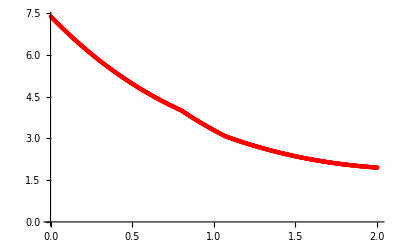

```mathematica
p14=ListPlot[tabT4,PlotStyle->Red]
```

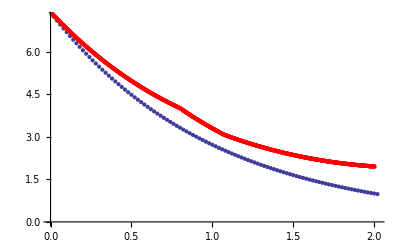

```mathematica
Show[p22,p14]
```